## FeynCalc Preamble

```mathematica
$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynHelpers 1.4.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

• Fermat by R. Lewis, if you are using the function FerSolve.

• QGRAF by P. Nogueira, if you are using functions that begin with QG.

• LoopTools by T. Hahn, if you are using functions that begin with LT.

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

## Important things needed for calculation

#### Limits for energy integrals and SM e+e- current

SM e-e current and photon prop squared

```mathematica
SMvert$ee$to$γ[μ_]:=I e GA[μ]
SM$γ$prop[μ_,ν_]:=-I MT[μ,ν]/ScalarProduct[q]
SM$vert$and$prop[ν_]:=Contract[SMvert$ee$to$γ[μ]SM$γ$prop[μ,ν]]//Simplify

ee$Curr$Sqr=DiracTrace[SM$vert$and$prop[ν].(GS[p$a]).SM$vert$and$prop[ρ].(GS[p$b]),DiracTraceEvaluate->True]//Expand
```

-(4 e^2 (ḡ)^νρ (OverBar[p$a]·OverBar[p$b]))/(q̄)^4+(4 e^2 OverBar[p$a]^ρ OverBar[p$b]^ν)/(q̄)^4+(4 e^2 OverBar[p$a]^ν OverBar[p$b]^ρ)/(q̄)^4

Energy integral limits

```mathematica
Eγ$LFV$min$mid=(s-((s-m$μ^2)^2-((s+m$μ^2-2Sqrt[s]Eμ)-2Sqrt[s]Sqrt[(Eμ^2-m$μ^2)])^2)/(4(s+m$μ^2-2Sqrt[s]Eμ)))/(2Sqrt[s])//Simplify;
Eγ$LFV$max$mid=(s-((s-m$μ^2)^2-((s+m$μ^2-2Sqrt[s]Eμ)+2Sqrt[s]Sqrt[(Eμ^2-m$μ^2)])^2)/(4(s+m$μ^2-2Sqrt[s]Eμ)))/(2Sqrt[s])//Simplify;
Eμ$LFV$min$mid=(s+m$μ^2-(s-2Sqrt[s]Eγ-m$μ^2)(2Sqrt[s]Eγ)/(s-2Sqrt[s]Eγ))/(2Sqrt[s])//Simplify;
Eμ$LFV$max$mid=(s+m$μ^2)/(2Sqrt[s])//Simplify;

Eγ$SM$min$mid=(s-(s^2-((s+m$μ^2-2Sqrt[s]Eμ)-m$μ^2-2Sqrt[s]Sqrt[Eμ^2-m$μ^2])^2)/(4(s+m$μ^2-2Sqrt[s]Eμ)))/(2Sqrt[s])//Simplify;
Eγ$SM$max$mid=(s-(s^2-((s+m$μ^2-2Sqrt[s]Eμ)-m$μ^2+2Sqrt[s]Sqrt[Eμ^2-m$μ^2])^2)/(4(s+m$μ^2-2Sqrt[s]Eμ)))/(2Sqrt[s])//Simplify;
Eμ$SM$min$mid=(4Sqrt[s-2Sqrt[s]Eγ](s+m$μ^2)+(Sqrt[s-2Sqrt[s]Eγ]+Sqrt[s-2Sqrt[s]Eγ-4m$μ^2])(s-2Sqrt[s]Eγ+Sqrt[s-2Sqrt[s]Eγ]Sqrt[s-2Sqrt[s]Eγ-4 m$μ^2]-2s) )/(8Sqrt[s]Sqrt[s-2Sqrt[s]Eγ])//Simplify;
Eμ$SM$max$mid=(4Sqrt[s-2Sqrt[s]Eγ](s+m$μ^2)+(Sqrt[s-2Sqrt[s]Eγ]-Sqrt[s-2Sqrt[s]Eγ-4 m$μ^2])(s-2Sqrt[s]Eγ-Sqrt[s-2Sqrt[s]Eγ]Sqrt[s-2Sqrt[s]Eγ-4 m$μ^2]-2 s ))/(8Sqrt[s]Sqrt[s-2Sqrt[s]Eγ])//Simplify;

Eγ$min$last=0;
Eμ$min$last=m$μ;
Eγ$LFV$max$last=((s-m$μ^2)/(2Sqrt[s]));
Eμ$LFV$max$last=((s+m$μ^2)/(2Sqrt[s]));
Eγ$SM$max$last=((s-4m$μ^2)/(2Sqrt[s]));
Eμ$SM$max$last=(Sqrt[s]/2);

Eγ$limits$LFV={Eγ$LFV$min$mid,Eγ$LFV$max$mid,Eγ$min$last,Eγ$LFV$max$last-0.01}
Eμ$limits$LFV={Eμ$LFV$min$mid,Eμ$LFV$max$mid,Eμ$min$last,Eμ$LFV$max$last-0.01}
Eγ$limits$SM={Eγ$SM$min$mid,Eγ$SM$max$mid,Eγ$min$last,Eγ$SM$max$last-0.01}
Eμ$limits$SM={Eμ$SM$min$mid,Eμ$SM$max$mid,Eμ$min$last,Eμ$SM$max$last-0.01}
```

{1/2 (-√(Eμ^2-m$μ^2)-Eμ+√s),1/2 (√(Eμ^2-m$μ^2)-Eμ+√s),0,(s-m$μ^2)/(2 √s)-0.01}

{(4 Eγ^2-4 Eγ √s+m$μ^2+s)/(2 (√s-2 Eγ)),(m$μ^2+s)/(2 √s),m$μ,(m$μ^2+s)/(2 √s)-0.01}

{(√s (2 Eμ-√s) (√(Eμ^2-m$μ^2)+Eμ-√s))/(2 (-2 Eμ √s+m$μ^2+s)),-(√s (2 Eμ-√s) (√(Eμ^2-m$μ^2)-Eμ+√s))/(2 (-2 Eμ √s+m$μ^2+s)),0,(s-4 m$μ^2)/(2 √s)-0.01}

{1/2 (Eγ (-(√(-2 Eγ √s-4 m$μ^2+s))/(√(s-2 Eγ √s))-1)+√s),1/2 (Eγ ((√(-2 Eγ √s-4 m$μ^2+s))/(√(s-2 Eγ √s))-1)+√s),m$μ,(√s)/2-0.01}

#### Variable substitutions and values

no mass dim

```mathematica
alpha=1/137;
e$set=Sqrt[4 Pi alpha];
SθW=Sqrt[0.2314];
gW$set=e$set/SθW;
β$W=4 mW$set^2/mH$set^2;
β$t=4mt$set^2/mH$set^2;
F$W=2+3β$W +3β$W(2-β$W)ArcSin[Sqrt[β$W]]^2;
F$t=-2β$t(1+(1-β$t)ArcSin[Sqrt[β$t]]^2);
FHγγ$set=(F$W+NC Qt^2 F$t)/.{NC->3,Qt->2/3};
FHγγ$sqr$set=Abs[FHγγ$set ComplexConjugate[FHγγ$set]];
```

mass dim of 2

```mathematica
s$set=(4+7)^2;
```

mass dim of -1

```mathematica
Fπγγ$set=1/(4 Pi^2 fπ$set+(s$set/(2 fπ$set)));
```

mass dim of 1

```mathematica
mu$set=0.000216;
md$set=0.000467;
ms$set=0.093;
mc$set=1.27;
mb$set=4.18;
mt$set=172.76;
me$set=0.000511;
mμ$set=0.1056583745;
mτ$set=1.77686;
mπ$set=0.139;
mρ$set=0.775;
mW$set=80.379;
mH$set=125.25;
vH$set =246;
fπ$set=0.130;
Λ$set=1000;
decay$of$ρ$to$ee=0.1478(4.72 10^(-5));
fρ$set=Sqrt[(3 mρ$set decay$of$ρ$to$ee)/(4π alpha^2)];
```

```mathematica
constVals={e->e$set,s->s$set,F$πγγ->Fπγγ$set,m$e->me$set,m$μ->mμ$set,m$τ->mτ$set,m$π->mπ$set,m$ρ->mρ$set,fπ->fπ$set,fρ->fρ$set,α->alpha,α$e->alpha,Qc->2/3,m$u->mu$set,m$d->md$set,m$s->ms$set,m$c->mc$set,m$b->mb$set,m$t->mt$set,m$W->mW$set,m$H->mH$set,F$Hγγ^2->FHγγ$sqr$set,gW->gW$set,v$H->vH$set};
```

```mathematica
d2CS$const=Sqrt[Eμ^2-m$μ^2] Eγ/(8(2Pi)^5 s);

essential$Vars$En={
ScalarProduct[p$a,p$b]->s/2,
ScalarProduct[q,p$a]->s/2,
ScalarProduct[q,p$b]->s/2,

ScalarProduct[p$a,k]->Sqrt[s]Eγ (1-Cos[θγ])/2,
ScalarProduct[p$b,k]->Sqrt[s]Eγ (1+Cos[θγ])/2,
ScalarProduct[q,k]->Sqrt[s]Eγ,

ScalarProduct[p$a,p$μ]->Sqrt[s] (Eμ-Sqrt[Eμ^2-m$μ^2]Cos[θμ])/2,
ScalarProduct[p$b,p$μ]->Sqrt[s] (Eμ+Sqrt[Eμ^2-m$μ^2]Cos[θμ])/2,
ScalarProduct[q,p$μ]->Sqrt[s]Eμ,

ScalarProduct[p$a,p$e]->s/2-Sqrt[s](Eμ+Eγ-Sqrt[Eμ^2-m$μ^2]Cos[θμ]-Eγ Cos[θγ])/2,
ScalarProduct[p$b,p$e]->s/2-Sqrt[s](Eμ+Eγ+Sqrt[Eμ^2-m$μ^2]Cos[θμ]+Eγ Cos[θγ])/2,
ScalarProduct[q,p$e]->s-Sqrt[s](Eμ+Eγ),

ScalarProduct[k,p$μ]->Sqrt[s](Eγ+Eμ)-s/2-m$μ^2/2,
ScalarProduct[p$μ,p$e]->s/2-Sqrt[s]Eγ-m$μ^2/2,
ScalarProduct[k,p$e]->s/2-Sqrt[s]Eμ+m$μ^2/2,

ScalarProduct[k]->0,ScalarProduct[p$a]->0,ScalarProduct[p$b]->0,
ScalarProduct[p$μ]->m$μ^2,ScalarProduct[p$e]->m$e^2,ScalarProduct[q]->s}
```

{OverBar[p$a]·OverBar[p$b]→s/2,OverBar[p$a]·q̄→s/2,OverBar[p$b]·q̄→s/2,k̄·OverBar[p$a]→1/2 Eγ √s (1-cos(θγ)),k̄·OverBar[p$b]→1/2 Eγ √s (cos(θγ)+1),k̄·q̄→Eγ √s,OverBar[p$a]·OverBar[p$μ]→1/2 √s (Eμ-√(Eμ^2-m$μ^2) cos(θμ)),OverBar[p$b]·OverBar[p$μ]→1/2 √s (√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$μ]·q̄→Eμ √s,OverBar[p$a]·OverBar[p$e]→s/2-1/2 √s (Eγ (-cos(θγ))+Eγ-√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$b]·OverBar[p$e]→s/2-1/2 √s (Eγ cos(θγ)+Eγ+√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$e]·q̄→s-√s (Eγ+Eμ),k̄·OverBar[p$μ]→√s (Eγ+Eμ)-m$μ^2/2-s/2,OverBar[p$e]·OverBar[p$μ]→-Eγ √s-m$μ^2/2+s/2,k̄·OverBar[p$e]→-Eμ √s+m$μ^2/2+s/2,(k̄)^2→0,OverBar[p$a]^2→0,OverBar[p$b]^2→0,OverBar[p$μ]^2→m$μ^2,OverBar[p$e]^2→m$e^2,(q̄)^2→s}

#### Important functions

```mathematica
single$triangle$loop$calc[term$type_]:=Module[{loop$term$1,loop$term$2},
FCClearScalarProducts[];
SPD[k]=0;

loop$term$1=(-1)I^3DiracTrace[(-I Q e GA[ν]).(GS[l]+m$l).(-I Q e GA[τ]).(GS[l+k]+m$l).term$type.(GS[l-q]+m$l),DiracTraceEvaluate->True];

loop$term$2=(-1)I^3DiracTrace[(-I Q e GA[τ]).(-GS[l]+m$l).(-I Q e GA[ν]).(-GS[l-q]+m$l).term$type.(-GS[l+k]+m$l),DiracTraceEvaluate->True];

ChangeDimension[PaXEvaluate[TID[ChangeDimension[Contract[loop$term$1+loop$term$2],D]FAD[{l,m$l},{l+k,m$l},{l-q,m$l}],l],l,PaXImplicitPrefactor-> 1/(2Pi)^D],4]/.{Pair[Momentum[k],LorentzIndex[τ]]->0,e^2->4 Pi α$e}]
```

```mathematica
d2CS$dEγdEμ$func[tri$loop_,tri$loop$CC_]:=Module[{LFV$Current=0,Amp$Sqr=0,Amp$Sqr$in$CoM=0,Amp$Sqr$no$q=0,Amp$Sqr$no$eps=0,angle$3int=0,d2CS$list={}},

LFV$Current=DiracTrace[-(tri$loop).(GS[p$μ]-m$μ).tri$loop$CC.(GS[p$e]+m$e),DiracTraceEvaluate->True];
Amp$Sqr=(1/4)(Contract[(ee$Curr$Sqr.LFV$Current)]//EpsEvaluate);

Amp$Sqr$in$CoM=(Amp$Sqr/.essential$Vars$En)//Expand;
Amp$Sqr$no$q=((Amp$Sqr$in$CoM)/.{Momentum[q]->Momentum[p$a]+Momentum[p$b],Momentum[p$e]->Momentum[p$a]+Momentum[p$b]-Momentum[k]-Momentum[p$μ]})//EpsEvaluate;
Amp$Sqr$no$eps=(Amp$Sqr$no$q)/.{Eps[Momentum[k],Momentum[p$a],Momentum[p$b],Momentum[p$μ]]->0};

angle$3int=d2CS$const Integrate[(Amp$Sqr$no$eps) Sin[θμ] Sin[θγ],{ϕμ,0,2Pi},{θμ,0,Pi},{θγ,0,Pi}];

Expand[angle$3int]]
```

```mathematica
axial$List$Manager[axial$loop_]:=Module[{axial$loop$list,a$list$1,a$list$2,a$list$3,a$list$3$k,a$list$4,a$list$4$k,a$list$5,axial$tensor$coeff$1,axial$tensor$coeff$2,axial$tensor$coeff$3,axial$tensor$coeff$4,axial$tensor$coeff$5,axial$tensor$coeff$6,axial$tensor$coeff$7,axial$tensor$structures$list},

axial$tensor$structures$list={
Eps[LorentzIndex[α],LorentzIndex[ν],LorentzIndex[τ],Momentum[q]],
Eps[LorentzIndex[α],LorentzIndex[ν],LorentzIndex[τ],Momentum[k]],
Eps[LorentzIndex[ν],LorentzIndex[τ],Momentum[k],Momentum[q]]Pair[LorentzIndex[α],Momentum[k]],
Eps[LorentzIndex[ν],LorentzIndex[τ],Momentum[k],Momentum[q]] Pair[LorentzIndex[α],Momentum[q]],
Eps[LorentzIndex[α],LorentzIndex[τ],Momentum[k],Momentum[q]]Pair[LorentzIndex[ν],Momentum[k]],
Eps[LorentzIndex[α],LorentzIndex[τ],Momentum[k],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]],
Eps[LorentzIndex[α],LorentzIndex[ν],Momentum[k],Momentum[q]]Pair[LorentzIndex[τ],Momentum[q]]
};

a$list$1=CoefficientList[axial$loop,axial$tensor$structures$list[[1]]];  
axial$tensor$coeff$1=a$list$1[[2]]//FullSimplify;
Print["1 tensor structure done"];

a$list$2=CoefficientList[a$list$1[[1]],axial$tensor$structures$list[[2]]];
axial$tensor$coeff$2=a$list$2[[2]]//FullSimplify;
Print["2 tensor structure done"];

a$list$3=CoefficientList[a$list$2[[1]],axial$tensor$structures$list[[3]][[1]]]; 
a$list$3$k=CoefficientList[a$list$3[[2]],axial$tensor$structures$list[[3]][[2]]]; 
axial$tensor$coeff$3=a$list$3$k[[2]]//FullSimplify;
Print["3 tensor structure done"];
axial$tensor$coeff$4=a$list$3$k[[1]]/(axial$tensor$structures$list[[4]][[2]])//Expand//FullSimplify;
Print["4 tensor structure done"];

a$list$4=CoefficientList[a$list$3[[1]],axial$tensor$structures$list[[5]][[1]]]; 
a$list$4$k=CoefficientList[a$list$4[[2]],axial$tensor$structures$list[[5]][[2]]]; 
axial$tensor$coeff$5=a$list$4$k[[2]]//FullSimplify;
Print["5 tensor structure done"];
axial$tensor$coeff$6=a$list$4$k[[1]]/(axial$tensor$structures$list[[6]][[2]])//Expand//FullSimplify;
Print["6 tensor structure done"];

a$list$5=CoefficientList[a$list$4[[1]],axial$tensor$structures$list[[7]][[1]]][[2]]/(axial$tensor$structures$list[[7]][[2]]);
axial$tensor$coeff$7=a$list$5//Expand//FullSimplify;
Print["7 tensor structure done"];

axial$loop$list={{axial$tensor$structures$list[[1]],axial$tensor$coeff$1},
{axial$tensor$structures$list[[2]],axial$tensor$coeff$2},
{axial$tensor$structures$list[[3]],axial$tensor$coeff$3},
{axial$tensor$structures$list[[4]],axial$tensor$coeff$4},
{axial$tensor$structures$list[[5]],axial$tensor$coeff$5},
{axial$tensor$structures$list[[6]],axial$tensor$coeff$6},
{axial$tensor$structures$list[[7]],axial$tensor$coeff$7}};

axial$loop$list]
```

```mathematica
CS$total$Numerical[diff$Sqr$CS_,u_,v_,u$limits_,v$limits_]:=Module[{CS$tot=0,CS$tot2=0,CS$total$list={},CS$total$list2={},i=1,nreps=10,MaxRec=10000},

If[ToString[diff$Sqr$CS]=="0",{CS$total$list, CS$total$list2}={0,0},
CS$tot:=NIntegrate[diff$Sqr$CS Boole[u$limits[[3]]<u<u$limits[[4]]],{v,v$limits[[3]],v$limits[[4]]},{u,u$limits[[1]],u$limits[[2]]},Method->"AdaptiveMonteCarlo", MaxRecursion->MaxRec];

CS$tot2:=NIntegrate[diff$Sqr$CS Boole[v$limits[[3]]<v<v$limits[[4]]],{u,u$limits[[3]],u$limits[[4]]},{v,v$limits[[1]],v$limits[[2]]},Method->"AdaptiveMonteCarlo", MaxRecursion->MaxRec];

Monitor[For[i=1,i≤nreps,i++,
AppendTo[CS$total$list,CS$tot];
AppendTo[CS$total$list2,CS$tot2];
];,ProgressIndicator[i,{1,nreps}]];];

{CS$total$list, CS$total$list2}]
```

```mathematica
Numerically$Solve[diff$Sqr$CS_,u_,v_,u$limits_,v$limits_]:=Module[{dCS$dv$Xtable={},dCS$du$Xtable={},dCS$dv$norm,dCS$du$norm,dCS$dv$Ytable={},dCS$du$Ytable={},dCS$dv$table={},dCS$du$table={},Nreps=100,MaxRec=10000},

dCS$dv$Xtable:=Table[v,{v,v$limits[[3]],v$limits[[4]],v$limits[[4]]/Nreps}];
dCS$du$Xtable:=Table[u,{u,u$limits[[3]],u$limits[[4]],u$limits[[4]]/Nreps}];

dCS$dv$norm:=NIntegrate[diff$Sqr$CS Boole[u$limits[[3]]<u<u$limits[[4]]],{u,u$limits[[1]],u$limits[[2]]},Method->"AdaptiveMonteCarlo", MaxRecursion->MaxRec];
dCS$du$norm:=NIntegrate[diff$Sqr$CS Boole[v$limits[[3]]<v<v$limits[[4]]],{v,v$limits[[1]],v$limits[[2]]},Method->"AdaptiveMonteCarlo", MaxRecursion->MaxRec];

dCS$dv$Ytable=Monitor[Table[dCS$dv$norm,{v,v$limits[[3]],v$limits[[4]],v$limits[[4]]/Nreps}],ProgressIndicator[v,{v$limits[[3]],v$limits[[4]]}]];
dCS$du$Ytable=Monitor[Table[dCS$du$norm,{u,u$limits[[3]],u$limits[[4]],u$limits[[4]]/Nreps}],ProgressIndicator[u,{u$limits[[3]],u$limits[[4]]}]];

dCS$dv$table=Transpose@{dCS$dv$Xtable,dCS$dv$Ytable};
dCS$du$table=Transpose@{dCS$du$Xtable,dCS$du$Ytable};

{dCS$dv$table,dCS$du$table}]
```

```mathematica
Get$dCS$Ratio[dCS$num_,dCS$den_]:=Module[{dCS$num$Xtable={},dCS$den$Xtable={},dCS$num$Ytable={},dCS$den$Ytable={},dCS$ratio$table={},i=1},

{dCS$num$Xtable,dCS$num$Ytable}=Transpose[dCS$num];
{dCS$den$Xtable,dCS$den$Ytable}=Transpose[dCS$den];

For[i=1,i≤Length[dCS$den$Ytable],i++,
If[dCS$den$Ytable[[i]]==0,AppendTo[dCS$ratio$table,{dCS$den$Xtable[[i]],0}],AppendTo[dCS$ratio$table,{dCS$den$Xtable[[i]],(dCS$num$Ytable[[i]])/(dCS$den$Ytable[[i]])}]]];

{dCS$ratio$table}]
```

```mathematica
Solve$And$Ratio$at$diff$Λ[diff$Sqr$CS$Num_,u$limits$Num_,v$limits$Num_,diff$Sqr$CS$Den_,u$limits$Den_,v$limits$Den_,u_,v_]:=Module[{dCS$dv$num={},dCS$du$num={},dCS$dv$den={},dCS$du$den={},dCS$du$ratio={},dCS$dv$ratio={}},

{dCS$dv$num,dCS$du$num}=Numerically$Solve[diff$Sqr$CS$Num,u,v,u$limits$Num,v$limits$Num];
{dCS$dv$den,dCS$du$den}=Numerically$Solve[diff$Sqr$CS$Den,u,v,u$limits$Den,v$limits$Den];

dCS$du$ratio=Get$dCS$Ratio[dCS$du$num,dCS$du$den];
dCS$dv$ratio=Get$dCS$Ratio[dCS$dv$num,dCS$dv$den];

Print["1 done"];

{dCS$du$ratio,dCS$dv$ratio}]
```

```mathematica
CS$at$diff$Λ[CS$tot_]:=Module[{CS$tot$list={},Max$Mag=6},

For[i=3,i≤Max$Mag,i++,
AppendTo[CS$tot$list,{10^i,Around[CS$tot[[1]]/.{Λ->10^i},CS$tot[[2]]/.{Λ->10^i}]}]];

CS$tot$list]
```

## LFV Cross Section Calculations

### Short distance μ-e-2γ CS

```mathematica
P$R =GA[6];
P$L =GA[7];
```

```mathematica
short$Dist[ν_,τ_]=(-1/Λ^3)FeynRule[(C$FFL P$L +C$FFR P$R) FieldStrength[ν,τ]FieldStrength[ν,τ]+(C$FFtL P$L + C$FFtR P$R)FieldStrength[ν,τ]FieldStrength[α1,β1]LC[ν,τ,α1,β1]/2,{QuantumField[GaugeField,{ν}][-q],QuantumField[GaugeField,{τ}][-k]}]//Expand
```

(4 ⅈ C$FFL (γ̄)^7 (ḡ)^ντ (k̄·q̄))/Λ^3-(4 ⅈ C$FFL (γ̄)^7 (k̄)^ν (q̄)^τ)/Λ^3+(4 ⅈ C$FFR (γ̄)^6 (ḡ)^ντ (k̄·q̄))/Λ^3-(4 ⅈ C$FFR (γ̄)^6 (k̄)^ν (q̄)^τ)/Λ^3+(4 ⅈ C$FFtL (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))/Λ^3+(4 ⅈ C$FFtR (γ̄)^6 (ϵ̄)^(ντ k̄ q̄))/Λ^3

```mathematica
short$Dist$d2$CS=d2CS$dEγdEμ$func[short$Dist[ν,τ],Expand[ComplexConjugate[short$Dist[τ,ρ]]]];
```

```mathematica
short$Dist$d2$CS//Length
```

14

```mathematica
SD$d2CS$coList=CoefficientList[Λ^6short$Dist$d2$CS,{C$FFL,C$FFR,C$FFtL,C$FFtR}];
```

```mathematica
SD$C$Λ$List={C$FFL^2,C$FFR^2,C$FFtL^2,C$FFtR^2,C$FFL C$FFR,C$FFL C$FFtL,C$FFL C$FFtR,C$FFR C$FFtL,C$FFR C$FFtR,C$FFtL C$FFtR}/Λ^6
```

{C$FFL^2/Λ^6,C$FFR^2/Λ^6,C$FFtL^2/Λ^6,C$FFtR^2/Λ^6,(C$FFL C$FFR)/Λ^6,(C$FFL C$FFtL)/Λ^6,(C$FFL C$FFtR)/Λ^6,(C$FFR C$FFtL)/Λ^6,(C$FFR C$FFtR)/Λ^6,(C$FFtL C$FFtR)/Λ^6}

```mathematica
SD$sqr$List={SD$d2CS$coList[[3]][[1]][[1]][[1]],SD$d2CS$coList[[1]][[3]][[1]][[1]],SD$d2CS$coList[[1]][[3]][[1]][[1]],SD$d2CS$coList[[1]][[3]][[1]][[1]],SD$d2CS$coList[[2]][[2]][[1]][[1]],SD$d2CS$coList[[2]][[1]][[2]][[1]],SD$d2CS$coList[[2]][[1]][[1]][[2]],SD$d2CS$coList[[1]][[2]][[2]][[1]],SD$d2CS$coList[[1]][[2]][[1]][[2]],SD$d2CS$coList[[1]][[1]][[2]][[2]]}//Simplify;
```

```mathematica
SD$mean$CS=SD$C$Λ$List Mean[CS$total$Numerical[SD$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
SD$stdDev$CS=SD$C$Λ$List StandardDeviation[CS$total$Numerical[SD$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(0.277693 C$FFL^2)/Λ^6-(2.67718×10^-6 C$FFL C$FFR)/Λ^6+(0.277285 C$FFR^2)/Λ^6+(0.277648 C$FFtL^2)/Λ^6+(1.77669×10^-6 C$FFtL C$FFtR)/Λ^6+(0.277288 C$FFtR^2)/Λ^6+0.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(0.00337546 C$FFL^2)/Λ^6+(2.90009×10^-8 C$FFL C$FFR)/Λ^6+(0.00362144 C$FFR^2)/Λ^6+(0.00382855 C$FFtL^2)/Λ^6+(2.38904×10^-8 C$FFtL C$FFtR)/Λ^6+(0.001839 C$FFtR^2)/Λ^6+0.

### Triangle loop CS

#### Triangle loop calculations

Vector and Tensor triangle loops are zero

```mathematica
vector$loop[τ_,ν_,α_]=single$triangle$loop$calc[I GA[α]];
vector$loop[τ,ν,α]//Length
```

0

```mathematica
σ$μν[μ_,ν_]:=(I/2)(GA[μ].GA[ν]-GA[ν].GA[μ]);
σ$μν$5[μ_,ν_]:=-(I/2)LeviCivita[γ1,γ2,μ,ν]σ$μν[γ1,γ2];
```

```mathematica
tensor$loop[τ_,ν_,α_,α2_]=single$triangle$loop$calc[I (σ$μν[α,α2]-σ$μν$5[α,α2])];
tensor$loop[τ,ν,α,α2]//Length
```

0

Scalar and Pseudoscalar triangle loops are nonzero

```mathematica
scalar$loop[τ_,ν_]=single$triangle$loop$calc[I]//FullSimplify;
```

```mathematica
S$triangle$loop[τ_,ν_]=scalar$loop[τ,ν][[{1,3,4,5,7}]]I$S
```

-(ⅈ α$e I$S Q^2 ((k̄)^ν (q̄)^τ-(ḡ)^ντ (k̄·q̄)))/(2 π)

```mathematica
I$S[m$l_]=scalar$loop[τ,ν][[{2,6,8,9}]]//Simplify;
```

```mathematica
I$S[Eγ_,s_,m$l_]=scalar$loop[τ,ν][[{6,8,9}]]/.essential$Vars$En//Simplify;
```

```mathematica
pseudoscalar$loop[τ_,ν_]=single$triangle$loop$calc[I GA[5]]//FullSimplify;
```

```mathematica
P$triangle$loop[τ_,ν_]=pseudoscalar$loop[τ,ν][[{1,3,4,5,6}]]I$P
```

(α$e I$P Q^2 (ϵ̄)^(ντ k̄ q̄))/(2 π)

```mathematica
I$P[m$l_]=pseudoscalar$loop[τ,ν][[{2,7,8}]]//Simplify;
```

```mathematica
I$P[Eγ_,s_,m$l_]=I$P[m$l]/.essential$Vars$En//Simplify;
```

```mathematica
SP$PR$triangle$loop[τ_,ν_]=(S$triangle$loop[τ,ν]+P$triangle$loop[τ,ν])/2 //Simplify
```

(α$e Q^2 (I$P (ϵ̄)^(ντ k̄ q̄)+ⅈ (I$S (ḡ)^ντ (k̄·q̄)-I$S (k̄)^ν (q̄)^τ)))/(4 π)

```mathematica
SP$PL$triangle$loop[τ_,ν_]=(S$triangle$loop[τ,ν]-P$triangle$loop[τ,ν])/2 //Simplify
```

-(α$e Q^2 (I$P (ϵ̄)^(ντ k̄ q̄)+ⅈ I$S ((k̄)^ν (q̄)^τ-(ḡ)^ντ (k̄·q̄))))/(4 π)

Axial triangle loops are nonzero and complicated, will separate into and substitute everything that’s not part of the Lorenze tensor structure

```mathematica
axial$loop[τ_,ν_,α_]=single$triangle$loop$calc[I GA[α].GA[5]]//Simplify;
axial$loop[τ,ν,α]//Length
```

8

```mathematica
A$loop$list[τ_,ν_,α_]=axial$List$Manager[axial$loop[τ,ν,α][[{5,6,7,8}]]];
```

1 tensor structure done

2 tensor structure done

3 tensor structure done

4 tensor structure done

5 tensor structure done

6 tensor structure done

7 tensor structure done

```mathematica
A$triangle$loop[τ_,ν_,α_]=axial$loop[τ,ν,α][[{1,2,3,4}]](A$loop$list[τ,ν,α][[1]][[1]]I$A$1+A$loop$list[τ,ν,α][[2]][[1]]I$A$2+A$loop$list[τ,ν,α][[3]][[1]]I$A$3+A$loop$list[τ,ν,α][[4]][[1]]I$A$4+A$loop$list[τ,ν,α][[5]][[1]]I$A$5+A$loop$list[τ,ν,α][[6]][[1]]I$A$6+A$loop$list[τ,ν,α][[7]][[1]]I$A$7)
```

(α$e Q^2 (I$A$1 (ϵ̄)^(αντ q̄)+I$A$2 (ϵ̄)^(αντ k̄)+I$A$3 (k̄)^α (ϵ̄)^(ντ k̄ q̄)+I$A$4 (q̄)^α (ϵ̄)^(ντ k̄ q̄)+I$A$5 (k̄)^ν (ϵ̄)^(ατ k̄ q̄)+I$A$6 (q̄)^ν (ϵ̄)^(ατ k̄ q̄)+I$A$7 (q̄)^τ (ϵ̄)^(αν k̄ q̄)))/(16 π)

```mathematica
I$A$1[m$l_]=A$loop$list[τ,ν,α][[1]][[2]]//Simplify;
I$A$2[m$l_]=A$loop$list[τ,ν,α][[2]][[2]]//Simplify;I$A$3[m$l_]=A$loop$list[τ,ν,α][[3]][[2]]//Simplify;I$A$4[m$l_]=A$loop$list[τ,ν,α][[4]][[2]]//Simplify;I$A$5[m$l_]=A$loop$list[τ,ν,α][[5]][[2]]//Simplify;I$A$6[m$l_]=A$loop$list[τ,ν,α][[6]][[2]]//Simplify;I$A$7[m$l_]=A$loop$list[τ,ν,α][[7]][[2]]//Simplify;
```

```mathematica
I$A$1[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[1]][[2]]/.essential$Vars$En//Simplify;
I$A$2[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[2]][[2]]/.essential$Vars$En//Simplify;
I$A$3[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[3]][[2]]/.essential$Vars$En//Simplify;
I$A$4[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[4]][[2]]/.essential$Vars$En//Simplify;
I$A$5[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[5]][[2]]/.essential$Vars$En//Simplify;
I$A$6[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[6]][[2]]/.essential$Vars$En//Simplify;
I$A$7[Eγ_,s_,m$l_]=A$loop$list[τ,ν,α][[7]][[2]]/.essential$Vars$En//Simplify;
```

This replaces the I’s in the above amplitudes with their whole function. 
Also, have a second set where it’s approximated with small m$l (mass of the fermion in the loop)

```mathematica
Triangle$piece$replacement[Eγ_,s_,m$l_,Q$set_]={
I$S->I$S[Eγ,s,m$l],I$S$CC->ComplexConjugate[I$S[Eγ,s,m$l]],
I$P->I$P[Eγ,s,m$l],I$P$CC->ComplexConjugate[I$P[Eγ,s,m$l]],

I$A$1->I$A$1[Eγ,s,m$l],I$A$1$CC->ComplexConjugate[I$A$1[Eγ,s,m$l]],
I$A$2->I$A$2[Eγ,s,m$l],I$A$2$CC->ComplexConjugate[I$A$2[Eγ,s,m$l]],
I$A$3->I$A$3[Eγ,s,m$l],I$A$3$CC->ComplexConjugate[I$A$3[Eγ,s,m$l]],
I$A$4->I$A$4[Eγ,s,m$l],I$A$4$CC->ComplexConjugate[I$A$4[Eγ,s,m$l]],
I$A$5->I$A$5[Eγ,s,m$l],I$A$5$CC->ComplexConjugate[I$A$5[Eγ,s,m$l]],
I$A$6->I$A$6[Eγ,s,m$l],I$A$6$CC->ComplexConjugate[I$A$6[Eγ,s,m$l]],
I$A$7->I$A$7[Eγ,s,m$l],I$A$7$CC->ComplexConjugate[I$A$7[Eγ,s,m$l]],

Q->Q$set};
```

```mathematica
Triangle$piece$rep$small$ml[Eγ_,s_,Q$set_]=Triangle$piece$replacement[Eγ,s,m$l,Q$set]/.{Log[(2 m$l^2-s+√(s (-4 m$l^2+s)))/(2 m$l^2)]->0,Log[(2 m$l^2-s+√(s (s-4 m$l^2)))/ m$l^2]->Log[2],Log[(2 m$l^2-2 Eγ √s-s+√((2 Eγ+√s) √s (-4 m$l^2+2 Eγ √s+s)))/(2 m$l^2)]->0,Log[(2 m$l^2-2 Eγ √s-s+√((2 Eγ √s+s) (-4 m$l^2+2 Eγ √s+s)))/(2 m$l^2)]->0,Log[(2 m$l^2-2 Eγ √s-s+√((2 Eγ √s+s) (-4 m$l^2+2 Eγ √s+s)))/m$l^2]->Log[2],Log[(2 m$l^2-2 Eγ √s-s+√((2 Eγ+√s) √s (-4 m$l^2+2 Eγ √s+s)))/m$l^2]->Log[2]};
```

```mathematica
I$to$I$CC={I$S->I$S$CC,I$P->I$P$CC,I$A$1->I$A$1$CC,I$A$2->I$A$2$CC,I$A$3->I$A$3$CC,I$A$4->I$A$4$CC,I$A$5->I$A$5$CC,I$A$6->I$A$6$CC,I$A$7->I$A$7$CC}
```

{I$S→I$S$CC,I$P→I$P$CC,I$A$1→I$A$1$CC,I$A$2→I$A$2$CC,I$A$3→I$A$3$CC,I$A$4→I$A$4$CC,I$A$5→I$A$5$CC,I$A$6→I$A$6$CC,I$A$7→I$A$7$CC}

#### Lepton loop

```mathematica
lepton$loop[τ_,ν_,α_]=(-1/Λ^2)(GA[α].P$L(C$l$AL A$triangle$loop[τ,ν,α]/2)+GA[α].P$R(C$l$AR A$triangle$loop[τ,ν,α]/2))//Expand
```

-(α$e C$l$AL I$A$1 Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$l$AL I$A$2 Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$l$AL I$A$3 Q^2 (γ̄)^α.(γ̄)^7 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AL I$A$4 Q^2 (γ̄)^α.(γ̄)^7 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AL I$A$5 Q^2 (γ̄)^α.(γ̄)^7 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AL I$A$6 Q^2 (γ̄)^α.(γ̄)^7 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AL I$A$7 Q^2 (γ̄)^α.(γ̄)^7 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$1 Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$2 Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$l$AR I$A$3 Q^2 (γ̄)^α.(γ̄)^6 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$4 Q^2 (γ̄)^α.(γ̄)^6 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$5 Q^2 (γ̄)^α.(γ̄)^6 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$6 Q^2 (γ̄)^α.(γ̄)^6 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$l$AR I$A$7 Q^2 (γ̄)^α.(γ̄)^6 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)

```mathematica
lepton$loop[τ,ν,α]//Length
```

14

```mathematica
lepton$loop$CC[τ_,ρ_,β_]=Expand[ComplexConjugate[lepton$loop[τ,ρ,β]]/.I$to$I$CC];
```

```mathematica
lepton$loop$d2$CS=d2CS$dEγdEμ$func[lepton$loop[τ,ν,α],lepton$loop$CC[τ,ρ,β]];
```

```mathematica
lepton$loop$d2$CS//Length
```

629

```mathematica
lep$d2CS$coList=CoefficientList[Λ^4lepton$loop$d2$CS,{C$l$AL,C$l$AR}];
```

```mathematica
lep$C$Λ$List={C$l$AL^2,C$l$AR^2,C$l$AL C$l$AR}/Λ^4
```

{C$l$AL^2/Λ^4,C$l$AR^2/Λ^4,(C$l$AL C$l$AR)/Λ^4}

```mathematica
lep$sqr$List={lep$d2CS$coList[[3]][[1]],lep$d2CS$coList[[1]][[3]],lep$d2CS$coList[[2]][[2]]}/.Triangle$piece$rep$small$ml[Eγ,s,-1]//Simplify;
```

```mathematica
lep$loop$mean$CS=(lep$C$Λ$List Mean[CS$total$Numerical[lep$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$l$AR->(C$ee-C$le),C$l$AL->(C$le-C$ll)}//Expand
lep$loop$stdDev$CS=(lep$C$Λ$List StandardDeviation[CS$total$Numerical[lep$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$l$AR->(C$ee-C$le),C$l$AL->(C$le-C$ll)}//Expand
```

(4.92628×10^-10 C$ee^2)/Λ^4-(9.8525×10^-10 C$ee C$le)/Λ^4-(7.20042×10^-15 C$ee C$ll)/Λ^4+(9.85894×10^-10 C$le^2)/Λ^4-(9.86538×10^-10 C$le C$ll)/Λ^4+(4.93272×10^-10 C$ll^2)/Λ^4

(3.58963×10^-12 C$ee^2)/Λ^4-(7.17919×10^-12 C$ee C$le)/Λ^4-(7.6592×10^-17 C$ee C$ll)/Λ^4+(7.12278×10^-12 C$le^2)/Λ^4-(7.06638×10^-12 C$le C$ll)/Λ^4+(3.53323×10^-12 C$ll^2)/Λ^4

#### Up-type light quark loop (u & c)

```mathematica
up$type$loop[τ_,ν_,α_]=(-NC/Λ^2)(GA[α].P$L(C$u$AL A$triangle$loop[τ,ν,α]/2)+GA[α].P$R(C$u$AR A$triangle$loop[τ,ν,α]/2)-P$R(C$lequ SP$PL$triangle$loop[τ,ν])-P$L(C$lequ$CC SP$PR$triangle$loop[τ,ν]))//Expand
```

(ⅈ α$e C$lequ I$S NC Q^2 (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2)-(α$e C$lequ I$P NC Q^2 (γ̄)^6 (ϵ̄)^(ντ k̄ q̄))/(4 π Λ^2)-(ⅈ α$e C$lequ I$S NC Q^2 (γ̄)^6 (k̄)^ν (q̄)^τ)/(4 π Λ^2)+(ⅈ α$e C$lequ$CC I$S NC Q^2 (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2)+(α$e C$lequ$CC I$P NC Q^2 (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))/(4 π Λ^2)-(ⅈ α$e C$lequ$CC I$S NC Q^2 (γ̄)^7 (k̄)^ν (q̄)^τ)/(4 π Λ^2)-(α$e C$u$AL I$A$1 NC Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$u$AL I$A$2 NC Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$u$AL I$A$3 NC Q^2 (γ̄)^α.(γ̄)^7 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AL I$A$4 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AL I$A$5 NC Q^2 (γ̄)^α.(γ̄)^7 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AL I$A$6 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AL I$A$7 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$1 NC Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$2 NC Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$u$AR I$A$3 NC Q^2 (γ̄)^α.(γ̄)^6 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$4 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$5 NC Q^2 (γ̄)^α.(γ̄)^6 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$6 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$u$AR I$A$7 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)

```mathematica
up$type$loop[τ,ν,α]//Length
```

20

```mathematica
up$type$loop$CC[τ_,ρ_,β_]=Expand[ComplexConjugate[up$type$loop[τ,ρ,β]]/.I$to$I$CC];
```

```mathematica
up$type$loop$d2$CS=d2CS$dEγdEμ$func[up$type$loop[τ,ν,α],up$type$loop$CC[τ,ρ,β]];
```

```mathematica
up$type$loop$d2$CS//Length
```

811

```mathematica
up$d2CS$coList=CoefficientList[Λ^4up$type$loop$d2$CS/.{C$lequ$CC->C$lequ},{C$u$AL,C$u$AR,C$lequ}];
```

```mathematica
up$C$Λ$List={C$u$AL^2,C$u$AR^2,C$lequ^2,C$u$AL C$u$AR,C$u$AL C$lequ,C$lequ C$u$AR}/Λ^4
```

{C$u$AL^2/Λ^4,C$u$AR^2/Λ^4,C$lequ^2/Λ^4,(C$u$AL C$u$AR)/Λ^4,(C$lequ C$u$AL)/Λ^4,(C$lequ C$u$AR)/Λ^4}

```mathematica
up$sqr$List=({up$d2CS$coList[[3]][[1]][[1]],up$d2CS$coList[[1]][[3]][[1]],up$d2CS$coList[[1]][[1]][[3]],up$d2CS$coList[[2]][[2]][[1]],up$d2CS$coList[[2]][[1]][[2]],up$d2CS$coList[[1]][[2]][[2]]}/.Triangle$piece$rep$small$ml[Eγ,s,2/3])/.{NC->1}//Simplify;
```

```mathematica
up$loop$mean$CS=(up$C$Λ$List Mean[CS$total$Numerical[up$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$u$AR->(C$eu-C$qe),C$u$AL->(C$lu-C$lq$1+C$lq$3)}//Expand
up$loop$stdDev$CS=(up$C$Λ$List StandardDeviation[CS$total$Numerical[up$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$u$AR->(C$eu-C$qe),C$u$AL->(C$lu-C$lq$1+C$lq$3)}//Expand
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(9.77038×10^-11 C$eu^2)/Λ^4-(1.41927×10^-15 C$eu C$lq$1)/Λ^4+(1.41927×10^-15 C$eu C$lq$3)/Λ^4+(1.41927×10^-15 C$eu C$lu)/Λ^4-(1.95408×10^-10 C$eu C$qe)/Λ^4+(1.8413×10^-11 C$lequ^2)/Λ^4+(9.72774×10^-11 C$lq$1^2)/Λ^4-(1.94555×10^-10 C$lq$1 C$lq$3)/Λ^4-(1.94555×10^-10 C$lq$1 C$lu)/Λ^4+(1.41927×10^-15 C$lq$1 C$qe)/Λ^4+(9.72774×10^-11 C$lq$3^2)/Λ^4+(1.94555×10^-10 C$lq$3 C$lu)/Λ^4-(1.41927×10^-15 C$lq$3 C$qe)/Λ^4+(9.72774×10^-11 C$lu^2)/Λ^4-(1.41927×10^-15 C$lu C$qe)/Λ^4+(9.77038×10^-11 C$qe^2)/Λ^4+0.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(8.40737×10^-13 C$eu^2)/Λ^4-(1.07688×10^-17 C$eu C$lq$1)/Λ^4+(1.07688×10^-17 C$eu C$lq$3)/Λ^4+(1.07688×10^-17 C$eu C$lu)/Λ^4-(1.68147×10^-12 C$eu C$qe)/Λ^4+(1.48508×10^-13 C$lequ^2)/Λ^4+(1.0679×10^-12 C$lq$1^2)/Λ^4-(2.1358×10^-12 C$lq$1 C$lq$3)/Λ^4-(2.1358×10^-12 C$lq$1 C$lu)/Λ^4+(1.07688×10^-17 C$lq$1 C$qe)/Λ^4+(1.0679×10^-12 C$lq$3^2)/Λ^4+(2.1358×10^-12 C$lq$3 C$lu)/Λ^4-(1.07688×10^-17 C$lq$3 C$qe)/Λ^4+(1.0679×10^-12 C$lu^2)/Λ^4-(1.07688×10^-17 C$lu C$qe)/Λ^4+(8.40737×10^-13 C$qe^2)/Λ^4+0.

#### Down-type light quark loop (d & s)

```mathematica
down$type$loop[τ_,ν_,α_]=(-NC/Λ^2)(GA[α].P$L(C$d$AL A$triangle$loop[τ,ν,α]/2)+GA[α].P$R(C$d$AR A$triangle$loop[τ,ν,α]/2)+P$R(C$ledq SP$PL$triangle$loop[τ,ν])+P$L(C$ledq$CC SP$PR$triangle$loop[τ,ν]))//Expand
```

-(α$e C$d$AL I$A$1 NC Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$d$AL I$A$2 NC Q^2 (γ̄)^α.(γ̄)^7 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$d$AL I$A$3 NC Q^2 (γ̄)^α.(γ̄)^7 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AL I$A$4 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AL I$A$5 NC Q^2 (γ̄)^α.(γ̄)^7 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AL I$A$6 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AL I$A$7 NC Q^2 (γ̄)^α.(γ̄)^7 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$1 NC Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$2 NC Q^2 (γ̄)^α.(γ̄)^6 (ϵ̄)^(αντ k̄))/(32 π Λ^2)-(α$e C$d$AR I$A$3 NC Q^2 (γ̄)^α.(γ̄)^6 (k̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$4 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^α (ϵ̄)^(ντ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$5 NC Q^2 (γ̄)^α.(γ̄)^6 (k̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$6 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^ν (ϵ̄)^(ατ k̄ q̄))/(32 π Λ^2)-(α$e C$d$AR I$A$7 NC Q^2 (γ̄)^α.(γ̄)^6 (q̄)^τ (ϵ̄)^(αν k̄ q̄))/(32 π Λ^2)-(ⅈ α$e C$ledq I$S NC Q^2 (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2)+(α$e C$ledq I$P NC Q^2 (γ̄)^6 (ϵ̄)^(ντ k̄ q̄))/(4 π Λ^2)+(ⅈ α$e C$ledq I$S NC Q^2 (γ̄)^6 (k̄)^ν (q̄)^τ)/(4 π Λ^2)-(ⅈ α$e C$ledq$CC I$S NC Q^2 (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2)-(α$e C$ledq$CC I$P NC Q^2 (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))/(4 π Λ^2)+(ⅈ α$e C$ledq$CC I$S NC Q^2 (γ̄)^7 (k̄)^ν (q̄)^τ)/(4 π Λ^2)

```mathematica
down$type$loop[τ,ν,α]//Length
```

20

```mathematica
down$type$loop$CC[τ_,ρ_,β_]=Expand[ComplexConjugate[down$type$loop[τ,ρ,β]]/.I$to$I$CC];
```

```mathematica
down$type$loop$d2$CS=d2CS$dEγdEμ$func[down$type$loop[τ,ν,α],down$type$loop$CC[τ,ρ,β]];
```

```mathematica
down$type$loop$d2$CS//Length
```

811

```mathematica
down$d2CS$coList=CoefficientList[Λ^4down$type$loop$d2$CS/.{C$ledq$CC->C$ledq},{C$d$AL,C$d$AR,C$ledq}];
```

```mathematica
down$C$Λ$List={C$d$AL^2,C$d$AR^2,C$ledq^2,C$d$AL C$d$AR,C$d$AL C$ledq,C$ledq C$d$AR}/Λ^4
```

{C$d$AL^2/Λ^4,C$d$AR^2/Λ^4,C$ledq^2/Λ^4,(C$d$AL C$d$AR)/Λ^4,(C$d$AL C$ledq)/Λ^4,(C$d$AR C$ledq)/Λ^4}

```mathematica
down$sqr$List=({down$d2CS$coList[[3]][[1]][[1]],down$d2CS$coList[[1]][[3]][[1]],down$d2CS$coList[[1]][[1]][[3]],down$d2CS$coList[[2]][[2]][[1]],down$d2CS$coList[[2]][[1]][[2]],down$d2CS$coList[[1]][[2]][[2]]}/.Triangle$piece$rep$small$ml[Eγ,s,-1/3])/.{NC->1}//Simplify;
```

```mathematica
down$loop$mean$CS=(down$C$Λ$List Mean[CS$total$Numerical[down$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$d$AR->(C$ed-C$qe),C$d$AL->(C$ld-C$lq$1-C$lq$3)}//Expand
down$loop$stdDev$CS=(down$C$Λ$List StandardDeviation[CS$total$Numerical[down$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total)/.{C$d$AR->(C$ed-C$qe),C$d$AL->(C$ld-C$lq$1-C$lq$3)}//Expand
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(6.0489×10^-12 C$ed^2)/Λ^4+(8.87137×10^-17 C$ed C$ld)/Λ^4-(8.87137×10^-17 C$ed C$lq$1)/Λ^4-(8.87137×10^-17 C$ed C$lq$3)/Λ^4-(1.20978×10^-11 C$ed C$qe)/Λ^4+(6.10918×10^-12 C$ld^2)/Λ^4-(1.22184×10^-11 C$ld C$lq$1)/Λ^4-(1.22184×10^-11 C$ld C$lq$3)/Λ^4-(8.87137×10^-17 C$ld C$qe)/Λ^4+(1.14995×10^-12 C$ledq^2)/Λ^4+(6.10918×10^-12 C$lq$1^2)/Λ^4+(1.22184×10^-11 C$lq$1 C$lq$3)/Λ^4+(8.87137×10^-17 C$lq$1 C$qe)/Λ^4+(6.10918×10^-12 C$lq$3^2)/Λ^4+(8.87137×10^-17 C$lq$3 C$qe)/Λ^4+(6.0489×10^-12 C$qe^2)/Λ^4+0.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(5.95334×10^-14 C$ed^2)/Λ^4+(1.12559×10^-18 C$ed C$ld)/Λ^4-(1.12559×10^-18 C$ed C$lq$1)/Λ^4-(1.12559×10^-18 C$ed C$lq$3)/Λ^4-(1.19067×10^-13 C$ed C$qe)/Λ^4+(4.07401×10^-14 C$ld^2)/Λ^4-(8.14801×10^-14 C$ld C$lq$1)/Λ^4-(8.14801×10^-14 C$ld C$lq$3)/Λ^4-(1.12559×10^-18 C$ld C$qe)/Λ^4+(1.63406×10^-14 C$ledq^2)/Λ^4+(4.07401×10^-14 C$lq$1^2)/Λ^4+(8.14801×10^-14 C$lq$1 C$lq$3)/Λ^4+(1.12559×10^-18 C$lq$1 C$qe)/Λ^4+(4.07401×10^-14 C$lq$3^2)/Λ^4+(1.12559×10^-18 C$lq$3 C$qe)/Λ^4+(5.95334×10^-14 C$qe^2)/Λ^4+0.

### Higgs propagator amps: H^3 mu e + (H i Dmu D) mu e

```mathematica
P$L =ChiralityProjector[-1];
P$R =ChiralityProjector[+1];
```

```mathematica
((v$H+QuantumField[h]). RightPartialD[ν].(QuantumField[h])-(I g/2)(v$H+QuantumField[h]).(-QuantumField[A,{ν}]SθW).(v$H+QuantumField[h])-(QuantumField[h]).LeftPartialD[ν].(v$H+QuantumField[h])+(I g/2)(v$H+QuantumField[h]).(-QuantumField[A,{ν}]SθW).(v$H+QuantumField[h]))//ExpandPartialD
```

h.(((∂)_ν h))-(((∂)_ν h)).h

```mathematica
FeynRule[(-1/Λ^2)(QuantumField[AntiQuarkField].GA[ν].((C$HL$1+C$HL$3)P$L +C$He P$R).QuantumField[QuarkField])(I/2)((v$H+QuantumField[h]). RightPartialD[ν].(QuantumField[h]))//ExpandPartialD,{QuantumField[QuarkField][p$μ],QuantumField[AntiQuarkField][p$e],QuantumField[h][q-k]}]//Simplify
```

-(ⅈ v$H (C$He (-(γ̄·(k̄-q̄))).(γ̄)^6+(C$HL$1+C$HL$3) (-(γ̄·(k̄-q̄))).(γ̄)^7))/(2 Λ^2)

```mathematica
higgs$prop=I/(ScalarProduct[q-k]-m$H^2)//ScalarProductExpand
effVert$H$to$μe=(-I(v$H^2/(2Λ^2))(C$eH$CC P$L +C$eH P$R)-I(v$H/Λ^2)Contract[FV[q-k,ν]GA[ν]].(C$He P$R +(C$HL$1+C$HL$3)P$L))//Simplify

effVert$H$to$2γ[ν_,τ_]=(-I 4 Pi α$e gW F$Hγγ/((4 Pi)^2 m$W))(ScalarProduct[k,q] MetricTensor[ν,τ] - FV[k,ν]FV[q,τ])
```

ⅈ/(-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2)

-((ⅈ v$H (C$eH v$H (γ̄)^6+C$eH$CC v$H (γ̄)^7+2 (γ̄·(q̄-k̄)).(C$He (γ̄)^6+(γ̄)^7 (C$HL$1+C$HL$3))))/(2 Λ^2))

-((ⅈ α$e F$Hγγ gW ((ḡ)^ντ (k̄·q̄)-(k̄)^ν (q̄)^τ))/(4 π m$W))

```mathematica
H$amp[ν_,τ_]=higgs$prop Contract[effVert$H$to$2γ[ν,τ].effVert$H$to$μe]//Expand
```

-(ⅈ α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(8 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))+(ⅈ α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (k̄)^ν (q̄)^τ)/(8 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))-(ⅈ α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(8 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))+(ⅈ α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (k̄)^ν (q̄)^τ)/(8 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))-(ⅈ α$e F$Hγγ gW v$H (ḡ)^ντ (k̄·q̄) (γ̄·(q̄-k̄)).(C$He (γ̄)^6+(γ̄)^7 (C$HL$1+C$HL$3)))/(4 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))+(ⅈ α$e F$Hγγ gW v$H (k̄)^ν (q̄)^τ (γ̄·(q̄-k̄)).(C$He (γ̄)^6+(γ̄)^7 (C$HL$1+C$HL$3)))/(4 π Λ^2 m$W (-2 (k̄·q̄)+(k̄)^2+(q̄)^2-m$H^2))

```mathematica
H$d2$CS=d2CS$dEγdEμ$func[H$amp[ν,τ],ComplexConjugate[H$amp[ρ,τ]]];
```

```mathematica
H$d2$CS//Length
```

41

```mathematica
H$d2CS$coList=CoefficientList[Λ^4H$d2$CS/.{C$eH$CC->C$eH},{C$eH,C$HL$1,C$HL$3,C$He}];
```

```mathematica
H$C$Λ$List={C$eH^2,C$HL$1^2,C$HL$3^2,C$He^2,C$eH C$HL$1,C$eH C$HL$3,C$eH C$He,C$HL$1 C$HL$3,C$HL$1 C$He,C$HL$3 C$He}/Λ^4
```

{C$eH^2/Λ^4,C$HL$1^2/Λ^4,C$HL$3^2/Λ^4,C$He^2/Λ^4,(C$eH C$HL$1)/Λ^4,(C$eH C$HL$3)/Λ^4,(C$eH C$He)/Λ^4,(C$HL$1 C$HL$3)/Λ^4,(C$He C$HL$1)/Λ^4,(C$He C$HL$3)/Λ^4}

```mathematica
H$sqr$List={H$d2CS$coList[[3]][[1]][[1]][[1]],H$d2CS$coList[[1]][[3]][[1]][[1]],H$d2CS$coList[[1]][[1]][[3]][[1]],H$d2CS$coList[[1]][[1]][[1]][[3]],H$d2CS$coList[[2]][[2]][[1]][[1]],H$d2CS$coList[[2]][[1]][[2]][[1]],H$d2CS$coList[[2]][[1]][[1]][[2]],H$d2CS$coList[[1]][[2]][[2]][[1]],H$d2CS$coList[[1]][[2]][[1]][[2]],H$d2CS$coList[[1]][[1]][[2]][[2]]}//Simplify;
```

```mathematica
H$mean$CS=(H$C$Λ$List Mean[CS$total$Numerical[H$sqr$List /. constVals, Eγ, Eμ, Eγ$limits$LFV /. constVals, Eμ$limits$LFV /. constVals][[1]]] //Total)//Expand
H$stdDev$CS=(H$C$Λ$List StandardDeviation[CS$total$Numerical[H$sqr$List /. constVals, Eγ, Eμ, Eγ$limits$LFV /. constVals, Eμ$limits$LFV /. constVals][[1]]] //Total)/.{C$eH$CC->C$eH}//Expand
```

(9.03146×10^-7 C$eH^2)/Λ^4-(7.79556×10^-10 C$eH C$He)/Λ^4-(7.74272×10^-10 C$eH C$HL$1)/Λ^4-(7.75362×10^-10 C$eH C$HL$3)/Λ^4+(3.351×10^-13 C$He^2)/Λ^4-(6.46622×10^-15 C$He C$HL$1)/Λ^4-(6.49271×10^-15 C$He C$HL$3)/Λ^4+(3.36284×10^-13 C$HL$1^2)/Λ^4+(6.73275×10^-13 C$HL$1 C$HL$3)/Λ^4+(3.35389×10^-13 C$HL$3^2)/Λ^4

(7.81073×10^-9 C$eH^2)/Λ^4+(6.42558×10^-12 C$eH C$He)/Λ^4+(9.53895×10^-12 C$eH C$HL$1)/Λ^4+(4.5363×10^-12 C$eH C$HL$3)/Λ^4+(2.33369×10^-15 C$He^2)/Λ^4+(6.21603×10^-17 C$He C$HL$1)/Λ^4+(4.94674×10^-17 C$He C$HL$3)/Λ^4+(4.20856×10^-15 C$HL$1^2)/Λ^4+(4.61409×10^-15 C$HL$1 C$HL$3)/Λ^4+(3.09868×10^-15 C$HL$3^2)/Λ^4

### Matching SMEFT to Rayleigh ops: Heavy quark loop (t&b) and Higgs prop

```mathematica
First$Simplification={(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[τ],Momentum[q]]-Pair[LorentzIndex[ν],LorentzIndex[τ]] Pair[Momentum[k],Momentum[q]])->MTkq ,Eps[LorentzIndex[ν],LorentzIndex[τ],Momentum[k],Momentum[q]]->Eντkq}
Second$Simplification={MTkq GA[6]->MTkq6,MTkq GA[7]->MTkq7,Eντkq GA[6]->Eντkq6,Eντkq GA[7]->Eντkq7,MTkq DiracGamma[6]->MTkq6,MTkq DiracGamma[7]->MTkq7,Eντkq DiracGamma[6]->Eντkq6,Eντkq DiracGamma[7]->Eντkq7,MTkq v$H^2 DiracGamma[6]->MTkq6 v$H^2,MTkq v$H^2 DiracGamma[7]->MTkq7 v$H^2};
```

{(k̄)^ν (q̄)^τ-(ḡ)^ντ (k̄·q̄)→MTkq,(ϵ̄)^(ντ k̄ q̄)→Eντkq}

```mathematica
Matching$RO$to$SMEFT[RayOps_,SMEFT_]:=Module[{SMEFT$simp,RO$simp,C$FFtR$match,C$FFtL$match,C$FFR$match,C$FFL$match},

SMEFT$simp=(((SMEFT//Simplify)/.First$Simplification)//Expand)/.Second$Simplification;
RO$simp=(((RayOps//Simplify)/.First$Simplification)//Expand)/.Second$Simplification;

C$FFtR$match=Solve[CoefficientList[RO$simp,Eντkq6][[2]]==CoefficientList[SMEFT$simp,Eντkq6][[2]],C$FFtR][[1]][[1]]//Expand;
C$FFtL$match=Solve[CoefficientList[RO$simp,Eντkq7][[2]]==CoefficientList[SMEFT$simp,Eντkq7][[2]],C$FFtL][[1]][[1]]//Expand;
C$FFR$match=Solve[CoefficientList[RO$simp,MTkq6][[2]]==CoefficientList[SMEFT$simp,MTkq6][[2]],C$FFR][[1]][[1]]//Expand;
C$FFL$match=Solve[CoefficientList[RO$simp,MTkq7][[2]]==CoefficientList[SMEFT$simp,MTkq7][[2]],C$FFL][[1]][[1]]//Expand;

{C$FFtR$match,C$FFtL$match,C$FFR$match,C$FFL$match}]
```

```mathematica
Heavy$quark$loop$simplification={
ScalarProduct[q]->0,
Pair[Momentum[q],LorentzIndex[ν]]->0,

I$S->Series[I$S[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$P->Series[I$P[m$l],{m$l,Infinity,1}]//Normal//Simplify,

I$A$1->Series[I$A$1[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$2->Series[I$A$2[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$3->Series[I$A$3[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$4->Series[I$A$4[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$5->Series[I$A$5[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$6->Series[I$A$6[m$l],{m$l,Infinity,1}]//Normal//Simplify,
I$A$7->Series[I$A$7[m$l],{m$l,Infinity,1}]//Normal//Simplify}
```

{(q̄)^2→0,(q̄)^ν→0,I$S→4/(3 m$l),I$P→-2/m$l,I$A$1→-8,I$A$2→8,I$A$3→0,I$A$4→0,I$A$5→0,I$A$6→0,I$A$7→0}

```mathematica
b$loop[τ_,ν_,α_]=(down$type$loop[τ,ν,α]/.Heavy$quark$loop$simplification)/.{Q->Qb,m$l->m$b}//Simplify
t$loop[τ_,ν_,α_]=(up$type$loop[τ,ν,α]/.Heavy$quark$loop$simplification)/.{Q->Qt,m$l->m$t}//Simplify
```

1/(12 π Λ^2 m$b)α$e NC Qb^2 (3 C$d$AL m$b (γ̄)^α.(γ̄)^7 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))+3 C$d$AR m$b (γ̄)^α.(γ̄)^6 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))-4 ⅈ C$ledq (γ̄)^6 (ḡ)^ντ (k̄·q̄)+4 ⅈ C$ledq (γ̄)^6 (k̄)^ν (q̄)^τ-6 C$ledq (γ̄)^6 (ϵ̄)^(ντ k̄ q̄)-4 ⅈ C$ledq$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄)+4 ⅈ C$ledq$CC (γ̄)^7 (k̄)^ν (q̄)^τ+6 C$ledq$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))

(α$e NC Qt^2 (4 ⅈ C$lequ (γ̄)^6 (ḡ)^ντ (k̄·q̄)-4 ⅈ C$lequ (γ̄)^6 (k̄)^ν (q̄)^τ+6 C$lequ (γ̄)^6 (ϵ̄)^(ντ k̄ q̄)+4 ⅈ C$lequ$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄)-4 ⅈ C$lequ$CC (γ̄)^7 (k̄)^ν (q̄)^τ-6 C$lequ$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄)+3 C$u$AL m$t (γ̄)^α.(γ̄)^7 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))+3 C$u$AR m$t (γ̄)^α.(γ̄)^6 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))))/(12 π Λ^2 m$t)

```mathematica
axial$term$to$zero={b$loop[τ,ν,α][[8]][[1;;2]]->0,t$loop[τ,ν,α][[8]][[1;;2]]->0}
```

{3 C$d$AL m$b (γ̄)^α.(γ̄)^7 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))+3 C$d$AR m$b (γ̄)^α.(γ̄)^6 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))→0,3 C$u$AL m$t (γ̄)^α.(γ̄)^7 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))+3 C$u$AR m$t (γ̄)^α.(γ̄)^6 ((ϵ̄)^(αντ q̄)-(ϵ̄)^(αντ k̄))→0}

```mathematica
HQ$loop[τ_,ν_]=(b$loop[τ,ν,α]+t$loop[τ,ν,α])/.axial$term$to$zero
```

(α$e NC Qb^2 (-4 ⅈ C$ledq (γ̄)^6 (ḡ)^ντ (k̄·q̄)+4 ⅈ C$ledq (γ̄)^6 (k̄)^ν (q̄)^τ-6 C$ledq (γ̄)^6 (ϵ̄)^(ντ k̄ q̄)-4 ⅈ C$ledq$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄)+4 ⅈ C$ledq$CC (γ̄)^7 (k̄)^ν (q̄)^τ+6 C$ledq$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄)))/(12 π Λ^2 m$b)+(α$e NC Qt^2 (4 ⅈ C$lequ (γ̄)^6 (ḡ)^ντ (k̄·q̄)-4 ⅈ C$lequ (γ̄)^6 (k̄)^ν (q̄)^τ+6 C$lequ (γ̄)^6 (ϵ̄)^(ντ k̄ q̄)+4 ⅈ C$lequ$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄)-4 ⅈ C$lequ$CC (γ̄)^7 (k̄)^ν (q̄)^τ-6 C$lequ$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄)))/(12 π Λ^2 m$t)

```mathematica
expanded$H$amp[ν_,τ_]=(Series[H$amp[ν,τ]/.{ScalarProduct[q]->0,ScalarProduct[k]->0,Pair[Momentum[q],LorentzIndex[ν]]->0},{m$H,Infinity,2}]//Normal)/.{DiracGamma[Momentum[-k+q]].(C$He DiracGamma[6]+(C$HL$1+C$HL$3) DiracGamma[7])->C$He (-m$μ GA[6])+(C$HL$1+C$HL$3)(-m$μ GA[7])}
```

-1/(8 π Λ^2 m$H^2 m$W)ⅈ (-α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (ḡ)^ντ (k̄·q̄)+α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (k̄)^ν (q̄)^τ-α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (ḡ)^ντ (k̄·q̄)+α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (k̄)^ν (q̄)^τ-2 α$e F$Hγγ gW v$H (ḡ)^ντ (k̄·q̄) (-C$He m$μ (γ̄)^6-m$μ (γ̄)^7 (C$HL$1+C$HL$3))+2 α$e F$Hγγ gW v$H (k̄)^ν (q̄)^τ (-C$He m$μ (γ̄)^6-m$μ (γ̄)^7 (C$HL$1+C$HL$3)))

```mathematica
Rayleigh$Op$matching=Matching$RO$to$SMEFT[short$Dist[ν,τ],(HQ$loop[τ,ν]+expanded$H$amp[ν,τ])]
```

{C$FFtR→(ⅈ α$e C$ledq Λ NC Qb^2)/(8 π m$b)-(ⅈ α$e C$lequ Λ NC Qt^2)/(8 π m$t),C$FFtL→(ⅈ α$e C$lequ$CC Λ NC Qt^2)/(8 π m$t)-(ⅈ α$e C$ledq$CC Λ NC Qb^2)/(8 π m$b),C$FFR→(α$e C$eH F$Hγγ gW Λ v$H^2)/(32 π m$H^2 m$W)-(α$e C$He F$Hγγ gW Λ m$μ v$H)/(16 π m$H^2 m$W)-(α$e C$ledq Λ NC Qb^2)/(12 π m$b)+(α$e C$lequ Λ NC Qt^2)/(12 π m$t),C$FFL→(α$e C$eH$CC F$Hγγ gW Λ v$H^2)/(32 π m$H^2 m$W)-(α$e C$HL$1 F$Hγγ gW Λ m$μ v$H)/(16 π m$H^2 m$W)-(α$e C$HL$3 F$Hγγ gW Λ m$μ v$H)/(16 π m$H^2 m$W)-(α$e C$ledq$CC Λ NC Qb^2)/(12 π m$b)+(α$e C$lequ$CC Λ NC Qt^2)/(12 π m$t)}

```mathematica
matched$short$Dist[ν_,τ_]=(short$Dist[ν,τ]/.Rayleigh$Op$matching)/.{NC->3,Qt->2/3,Qb->-1/3}//Expand
```

(ⅈ α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(8 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$eH F$Hγγ gW v$H^2 (γ̄)^6 (k̄)^ν (q̄)^τ)/(8 π Λ^2 m$H^2 m$W)+(ⅈ α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(8 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$eH$CC F$Hγγ gW v$H^2 (γ̄)^7 (k̄)^ν (q̄)^τ)/(8 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$He F$Hγγ gW m$μ v$H (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2 m$H^2 m$W)+(ⅈ α$e C$He F$Hγγ gW m$μ v$H (γ̄)^6 (k̄)^ν (q̄)^τ)/(4 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$HL$1 F$Hγγ gW m$μ v$H (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2 m$H^2 m$W)+(ⅈ α$e C$HL$1 F$Hγγ gW m$μ v$H (γ̄)^7 (k̄)^ν (q̄)^τ)/(4 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$HL$3 F$Hγγ gW m$μ v$H (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(4 π Λ^2 m$H^2 m$W)+(ⅈ α$e C$HL$3 F$Hγγ gW m$μ v$H (γ̄)^7 (k̄)^ν (q̄)^τ)/(4 π Λ^2 m$H^2 m$W)-(ⅈ α$e C$ledq (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(9 π Λ^2 m$b)+(ⅈ α$e C$ledq (γ̄)^6 (k̄)^ν (q̄)^τ)/(9 π Λ^2 m$b)-(α$e C$ledq (γ̄)^6 (ϵ̄)^(ντ k̄ q̄))/(6 π Λ^2 m$b)-(ⅈ α$e C$ledq$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(9 π Λ^2 m$b)+(ⅈ α$e C$ledq$CC (γ̄)^7 (k̄)^ν (q̄)^τ)/(9 π Λ^2 m$b)+(α$e C$ledq$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))/(6 π Λ^2 m$b)+(4 ⅈ α$e C$lequ (γ̄)^6 (ḡ)^ντ (k̄·q̄))/(9 π Λ^2 m$t)-(4 ⅈ α$e C$lequ (γ̄)^6 (k̄)^ν (q̄)^τ)/(9 π Λ^2 m$t)+(2 α$e C$lequ (γ̄)^6 (ϵ̄)^(ντ k̄ q̄))/(3 π Λ^2 m$t)+(4 ⅈ α$e C$lequ$CC (γ̄)^7 (ḡ)^ντ (k̄·q̄))/(9 π Λ^2 m$t)-(4 ⅈ α$e C$lequ$CC (γ̄)^7 (k̄)^ν (q̄)^τ)/(9 π Λ^2 m$t)-(2 α$e C$lequ$CC (γ̄)^7 (ϵ̄)^(ντ k̄ q̄))/(3 π Λ^2 m$t)

```mathematica
matched$short$Dist$d2$CS=d2CS$dEγdEμ$func[matched$short$Dist[ν,τ],Expand[ComplexConjugate[matched$short$Dist[ρ,τ]]]];
```

```mathematica
matched$short$Dist$d2$CS//Length
```

95

```mathematica
matched$SD$d2CS$coList=CoefficientList[Λ^4matched$short$Dist$d2$CS/.{C$lequ$CC->C$lequ,C$ledq$CC->C$ledq,C$eH$CC->C$eH},{C$lequ,C$ledq,C$eH,C$He,C$HL$1,C$HL$3}];
```

```mathematica
matched$SD$C$Λ$List={C$lequ^2,C$ledq^2,C$eH^2,C$He^2,C$HL$1^2,C$HL$3^2,C$lequ C$ledq,C$lequ C$eH,C$lequ C$He,C$lequ C$HL$1,C$lequ C$HL$3,C$ledq C$eH,C$ledq C$He,C$ledq C$HL$1,C$ledq C$HL$3,C$eH C$He,C$eH C$HL$1,C$eH C$HL$3,C$He C$HL$1,C$He C$HL$3,C$HL$1 C$HL$3}/Λ^4
```

{C$lequ^2/Λ^4,C$ledq^2/Λ^4,C$eH^2/Λ^4,C$He^2/Λ^4,C$HL$1^2/Λ^4,C$HL$3^2/Λ^4,(C$ledq C$lequ)/Λ^4,(C$eH C$lequ)/Λ^4,(C$He C$lequ)/Λ^4,(C$HL$1 C$lequ)/Λ^4,(C$HL$3 C$lequ)/Λ^4,(C$eH C$ledq)/Λ^4,(C$He C$ledq)/Λ^4,(C$HL$1 C$ledq)/Λ^4,(C$HL$3 C$ledq)/Λ^4,(C$eH C$He)/Λ^4,(C$eH C$HL$1)/Λ^4,(C$eH C$HL$3)/Λ^4,(C$He C$HL$1)/Λ^4,(C$He C$HL$3)/Λ^4,(C$HL$1 C$HL$3)/Λ^4}

```mathematica
matched$SD$sqr$List={matched$SD$d2CS$coList[[3]][[1]][[1]][[1]][[1]][[1]],matched$SD$d2CS$coList[[1]][[3]][[1]][[1]][[1]][[1]],matched$SD$d2CS$coList[[1]][[1]][[3]][[1]][[1]][[1]],matched$SD$d2CS$coList[[1]][[1]][[1]][[3]][[1]][[1]],matched$SD$d2CS$coList[[1]][[1]][[1]][[1]][[3]][[1]],matched$SD$d2CS$coList[[1]][[1]][[1]][[1]][[3]][[1]],matched$SD$d2CS$coList[[2]][[2]][[1]][[1]][[1]][[1]],matched$SD$d2CS$coList[[2]][[1]][[2]][[1]][[1]][[1]],matched$SD$d2CS$coList[[2]][[1]][[1]][[2]][[1]][[1]],matched$SD$d2CS$coList[[2]][[1]][[1]][[1]][[2]][[1]],matched$SD$d2CS$coList[[2]][[1]][[1]][[1]][[1]][[2]],matched$SD$d2CS$coList[[1]][[2]][[2]][[1]][[1]][[1]],matched$SD$d2CS$coList[[1]][[2]][[1]][[2]][[1]][[1]],matched$SD$d2CS$coList[[1]][[2]][[1]][[1]][[2]][[1]],matched$SD$d2CS$coList[[1]][[2]][[1]][[1]][[1]][[2]],matched$SD$d2CS$coList[[1]][[1]][[2]][[2]][[1]][[1]],matched$SD$d2CS$coList[[1]][[1]][[2]][[1]][[2]][[1]],matched$SD$d2CS$coList[[1]][[1]][[2]][[1]][[1]][[2]],matched$SD$d2CS$coList[[1]][[1]][[1]][[2]][[2]][[1]],matched$SD$d2CS$coList[[1]][[1]][[1]][[2]][[1]][[2]],matched$SD$d2CS$coList[[1]][[1]][[1]][[1]][[2]][[2]]}//Simplify;
```

```mathematica
matched$SD$mean$CS=matched$SD$C$Λ$List Mean[CS$total$Numerical[(matched$SD$sqr$List/.constVals)/.{F$Hγγ->Abs[FHγγ$set]},Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
matched$SD$stdDev$CS=matched$SD$C$Λ$List StandardDeviation[CS$total$Numerical[(matched$SD$sqr$List/.constVals)/.{F$Hγγ->Abs[FHγγ$set]},Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
```

(9.04034×10^-7 C$eH^2)/Λ^4-(7.72369×10^-10 C$eH C$He)/Λ^4-(7.75762×10^-10 C$eH C$HL$1)/Λ^4-(7.74189×10^-10 C$eH C$HL$3)/Λ^4-(1.77889×10^-8 C$eH C$ledq)/Λ^4+(1.72617×10^-9 C$eH C$lequ)/Λ^4+(3.34004×10^-13 C$He^2)/Λ^4-(3.19254×10^-18 C$He C$HL$1)/Λ^4-(3.19349×10^-18 C$He C$HL$3)/Λ^4+(7.68041×10^-12 C$He C$ledq)/Λ^4-(7.41131×10^-13 C$He C$lequ)/Λ^4+(3.32256×10^-13 C$HL$1^2)/Λ^4+(6.64813×10^-13 C$HL$1 C$HL$3)/Λ^4+(7.62765×10^-12 C$HL$1 C$ledq)/Λ^4-(7.41723×10^-13 C$HL$1 C$lequ)/Λ^4+(3.32852×10^-13 C$HL$3^2)/Λ^4+(7.66946×10^-12 C$HL$3 C$ledq)/Λ^4-(7.36593×10^-13 C$HL$3 C$lequ)/Λ^4+(2.87246×10^-10 C$ledq^2)/Λ^4-(5.57292×10^-11 C$ledq C$lequ)/Λ^4+(2.67693×10^-12 C$lequ^2)/Λ^4

(8.45168×10^-9 C$eH^2)/Λ^4+(8.741×10^-12 C$eH C$He)/Λ^4+(6.70481×10^-12 C$eH C$HL$1)/Λ^4+(7.15599×10^-12 C$eH C$HL$3)/Λ^4+(1.85522×10^-10 C$eH C$ledq)/Λ^4+(1.91413×10^-11 C$eH C$lequ)/Λ^4+(3.2969×10^-15 C$He^2)/Λ^4+(3.09001×10^-20 C$He C$HL$1)/Λ^4+(2.63831×10^-20 C$He C$HL$3)/Λ^4+(6.30582×10^-14 C$He C$ledq)/Λ^4+(8.05944×10^-15 C$He C$lequ)/Λ^4+(3.21383×10^-15 C$HL$1^2)/Λ^4+(6.95291×10^-15 C$HL$1 C$HL$3)/Λ^4+(6.01588×10^-14 C$HL$1 C$ledq)/Λ^4+(4.98565×10^-15 C$HL$1 C$lequ)/Λ^4+(3.51655×10^-15 C$HL$3^2)/Λ^4+(7.04846×10^-14 C$HL$3 C$ledq)/Λ^4+(5.68446×10^-15 C$HL$3 C$lequ)/Λ^4+(2.85987×10^-12 C$ledq^2)/Λ^4+(4.0907×10^-13 C$ledq C$lequ)/Λ^4+(2.80191×10^-14 C$lequ^2)/Λ^4

### Long distance μ-e-2γ eff vert via π0

```mathematica
P$L =ChiralityProjector[-1];
P$R =ChiralityProjector[+1];
```

```mathematica
FeynRule[-(QuantumField[AntiQuarkField].GA[ν].(C$π$AL P$L +C$π$AR P$R).QuantumField[QuarkField]),{QuantumField[QuarkField][p$μ],QuantumField[AntiQuarkField][p$e]}]//Simplify
```

-ⅈ (C$π$AL (γ̄)^ν.(γ̄)^7+C$π$AR (γ̄)^ν.(γ̄)^6)

```mathematica
pion$prop=I/(ScalarProduct[q-k]-m$π^2)
effVert$π$to$μe=-I(I fπ/Λ^2)Contract[FV[q-k,ν]GA[ν]].(C$π$AL P$L +C$π$AR P$R)//Simplify

effVert$π$to$2γ[ν_,τ_]=(-I e^2 F$πγγ)LC[ν,τ,β1,β2]FV[k,β1]FV[q,β2]
```

ⅈ/((q̄-k̄)^2-m$π^2)

(fπ (γ̄·(q̄-k̄)).(C$π$AL (γ̄)^7+C$π$AR (γ̄)^6))/Λ^2

-ⅈ e^2 F$πγγ (k̄)^β1 (q̄)^β2 (ϵ̄)^ντβ1β2

```mathematica
long$Dist$π0[ν_,τ_]=pion$prop Contract[effVert$π$to$2γ[ν,τ].effVert$π$to$μe]//Expand
```

(e^2 fπ F$πγγ (ϵ̄)^(ντ k̄ q̄) (γ̄·(q̄-k̄)).(C$π$AL (γ̄)^7+C$π$AR (γ̄)^6))/(Λ^2 ((q̄-k̄)^2-m$π^2))

```mathematica
long$Dist$π0$d2$CS=d2CS$dEγdEμ$func[long$Dist$π0[ν,τ],ComplexConjugate[long$Dist$π0[ρ,τ]]];
```

```mathematica
long$Dist$π0$d2$CS//Length
```

8

```mathematica
long$Dist$π0$d2$CS/.{m$e->0}//Simplify
```

-(e^6 Eγ^3 fπ^2 F$πγγ^2 m$μ^2 (C$π$AL^2+C$π$AR^2) √(Eμ^2-m$μ^2) (2 Eγ √s+m$μ^2-s))/(48 π^4 Λ^4 s (2 Eγ √s+m$π^2-s)^2)

```mathematica
LD$π0$d2CS$coList=CoefficientList[Λ^4long$Dist$π0$d2$CS,{C$π$AL,C$π$AR}];
```

```mathematica
LD$π0$C$Λ$List={C$π$AL^2,C$π$AR^2,C$π$AL C$π$AR}/Λ^4
```

{C$π$AL^2/Λ^4,C$π$AR^2/Λ^4,(C$π$AL C$π$AR)/Λ^4}

```mathematica
LD$π0$sqr$List={LD$π0$d2CS$coList[[3]][[1]],LD$π0$d2CS$coList[[1]][[3]],LD$π0$d2CS$coList[[2]][[2]]}//Simplify;
```

```mathematica
LD$π0$mean$CS=LD$π0$C$Λ$List Mean[CS$total$Numerical[LD$π0$sqr$List /. constVals, Eγ, Eμ, Eγ$limits$LFV /. constVals, Eμ$limits$LFV /. constVals][[1]]] // Total // Expand
LD$π0$stdDev$CS=LD$π0$C$Λ$List StandardDeviation[CS$total$Numerical[LD$π0$sqr$List /. constVals, Eγ, Eμ, Eγ$limits$LFV /. constVals, Eμ$limits$LFV /. constVals][[1]]] // Total // Expand
```

(5.91507×10^-16 C$π$AL^2)/Λ^4-(1.16318×10^-17 C$π$AL C$π$AR)/Λ^4+(5.92295×10^-16 C$π$AR^2)/Λ^4

(6.02429×10^-18 C$π$AL^2)/Λ^4+(1.25961×10^-19 C$π$AL C$π$AR)/Λ^4+(5.6163×10^-18 C$π$AR^2)/Λ^4

### Long distance μ-e-2γ eff vert via ρ0

```mathematica
P$L =ChiralityProjector[-1];
P$R =ChiralityProjector[+1];
```

```mathematica
(e /f$ρ)((fρ m$ρ + ScalarProduct[q])MT[ν,σ]-FV[q,ν]FV[q,σ]);
-I(MT[σ,λ]-FV[q,σ]FV[q,λ]/m$ρ^2)/(ScalarProduct[q]-m$ρ^2);
```

```mathematica
FeynRule[(e/fρ )((1/2)FieldStrength[ν,σ].(RightPartialD[ν].QuantumField[B,{σ}]-RightPartialD[σ].QuantumField[B,{ν}])+QuantumField[B,{σ}].QuantumField[GaugeField,{ν}].MT[σ,ν]m$ρ^2),{QuantumField[GaugeField,{ν}][q],QuantumField[B,{σ}][q]}]//Simplify
```

(ⅈ e ((m$ρ^2-(q̄)^2) (ḡ)^νσ+(q̄)^ν (q̄)^σ))/fρ

```mathematica
FeynRule[-(1/Λ^2)(QuantumField[AntiQuarkField].GA[λ].(C$ρ$VL P$L +C$ρ$VR P$R).QuantumField[QuarkField]),{QuantumField[QuarkField][q$μ],QuantumField[AntiQuarkField][q$e]}]//Simplify
```

-(ⅈ (C$ρ$VL (γ̄)^(FCGV(li13154)).(γ̄)^7+C$ρ$VR (γ̄)^(FCGV(li13154)).(γ̄)^6))/Λ^2

```mathematica
effVert$ρ$to$γ[ν_,σ_]:=(-I e MT[ν,σ](ScalarProduct[q]-m$ρ^2)fρ/m$ρ)
effVert$ρ$to$γ[ν,σ]

rho$prop[σ_,λ_]:=-I MT[σ,λ]/(ScalarProduct[q]-m$ρ^2)
rho$prop[σ,λ]

effVert$ρ$to$μe[λ_]:=(m$ρ fρ)(-I/Λ^2) GA[λ].(C$ρ$VL P$L+C$ρ$VR P$R)//Simplify
effVert$ρ$to$μe[λ]
```

-(ⅈ e fρ ((q̄)^2-m$ρ^2) (ḡ)^νσ)/m$ρ

-((ⅈ (ḡ)^λσ)/((q̄)^2-m$ρ^2))

-((ⅈ fρ m$ρ (γ̄)^λ.(C$ρ$VL (γ̄)^7+C$ρ$VR (γ̄)^6))/Λ^2)

```mathematica
q$μ$prop=I(GS[q$μ]+m$μ)/(ScalarProduct[q$μ]-m$μ^2)
q$e$prop=I(GS[q$e]+m$e)/(ScalarProduct[q$e])
```

(ⅈ (γ̄·OverBar[q$μ]+m$μ))/(OverBar[q$μ]^2-m$μ^2)

(ⅈ (γ̄·OverBar[q$e]+m$e))/OverBar[q$e]^2

```mathematica
effVert$longDist$ρ0$A[ν_,τ_]:=Contract[effVert$ρ$to$γ[ν,σ] rho$prop[σ,λ](I e GA[τ]).q$e$prop. effVert$ρ$to$μe[λ]]/.{Momentum[q$e]->Momentum[p$e]+Momentum[k],Momentum[q$μ]->Momentum[p$μ]}
effVert$longDist$ρ0$B[ν_,τ_]:=Contract[effVert$ρ$to$γ[ν,σ] rho$prop[σ,λ]effVert$ρ$to$μe[λ].q$μ$prop.(I e GA[τ]) ]/.{Momentum[q$e]->Momentum[p$e],Momentum[q$μ]->Momentum[p$e]-Momentum[q]}
effVert$longDist$ρ0$A[ν,τ]//Simplify
effVert$longDist$ρ0$B[ν,τ]//Simplify
```

-(ⅈ e^2 fρ^2 (γ̄)^τ.(γ̄·k̄+γ̄·OverBar[p$e]+m$e).(γ̄)^ν.(C$ρ$VL (γ̄)^7+C$ρ$VR (γ̄)^6))/(Λ^2 (k̄+OverBar[p$e])^2)

(ⅈ e^2 fρ^2 (γ̄)^ν.(C$ρ$VL (γ̄)^7+C$ρ$VR (γ̄)^6).(γ̄·OverBar[p$e]-γ̄·q̄+m$μ).(γ̄)^τ)/(Λ^2 (m$μ^2-(OverBar[p$e]-q̄)^2))

```mathematica
longDist$ρ0[ν_,τ_]=ComplexConjugate[ComplexConjugate[((effVert$longDist$ρ0$A[ν,τ]+effVert$longDist$ρ0$B[ν,τ])//ScalarProductExpand)/.{ScalarProduct[k]->0,ScalarProduct[p$μ]->m$μ^2,ScalarProduct[p$e]->0}//Simplify]]
```

(ⅈ e^2 fρ^2 (γ̄)^ν.(C$ρ$VL (γ̄)^7+C$ρ$VR (γ̄)^6).(γ̄·OverBar[p$e]-γ̄·q̄+m$μ).(γ̄)^τ)/(Λ^2 (2 (OverBar[p$e]·q̄)-(q̄)^2+m$μ^2))-(ⅈ e^2 fρ^2 (γ̄)^τ.(γ̄·k̄+γ̄·OverBar[p$e]+m$e).(γ̄)^ν.(C$ρ$VL (γ̄)^7+C$ρ$VR (γ̄)^6))/(2 Λ^2 (k̄·OverBar[p$e]))

```mathematica
long$Dist$ρ0$d2$CS=d2CS$dEγdEμ$func[longDist$ρ0[ν,τ],Expand[ComplexConjugate[longDist$ρ0[ρ,τ]]]];
```

```mathematica
long$Dist$ρ0$d2$CS//Length
```

164

```mathematica
LD$ρ0$d2CS$coList=CoefficientList[Λ^4long$Dist$ρ0$d2$CS,{C$ρ$VL,C$ρ$VR}];
```

```mathematica
LD$ρ0$C$Λ$List={C$ρ$VL^2,C$ρ$VR^2,C$ρ$VL C$ρ$VR}/Λ^4
```

{C$ρ$VL^2/Λ^4,C$ρ$VR^2/Λ^4,(C$ρ$VL C$ρ$VR)/Λ^4}

```mathematica
LD$ρ0$sqr$List={LD$ρ0$d2CS$coList[[3]][[1]],LD$ρ0$d2CS$coList[[1]][[3]],LD$ρ0$d2CS$coList[[2]][[2]]}//Simplify;
```

```mathematica
LD$ρ0$mean$CS=LD$ρ0$C$Λ$List Mean[CS$total$Numerical[LD$ρ0$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
LD$ρ0$stdDev$CS=LD$ρ0$C$Λ$List StandardDeviation[CS$total$Numerical[LD$ρ0$sqr$List/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]//Total//Expand
```

(1.51823×10^-10 C$ρ$VL^2)/Λ^4+(2.83405×10^-16 C$ρ$VL C$ρ$VR)/Λ^4+(1.46963×10^-10 C$ρ$VR^2)/Λ^4

(5.50868×10^-12 C$ρ$VL^2)/Λ^4+(8.35132×10^-18 C$ρ$VL C$ρ$VR)/Λ^4+(4.54809×10^-12 C$ρ$VR^2)/Λ^4

## SM Cross Section Calculations

### e+ e- -> μ+ μ- Squared Amplitude and cross section

SM mu-mu current

```mathematica
SMvert$μμ[μ_]:=I e GA[μ]
μμ$Curr$Sqr=DiracTrace[SMvert$μμ[ν].(GS[p$1]-m$μ).ComplexConjugate[SMvert$μμ[ρ]].(GS[p$2]+m$μ),DiracTraceEvaluate->True]
```

-4 e^2 (m$μ^2 (ḡ)^νρ+(ḡ)^νρ (OverBar[p$1]·OverBar[p$2])-OverBar[p$1]^ρ OverBar[p$2]^ν-OverBar[p$1]^ν OverBar[p$2]^ρ)

```mathematica
ee$to$μμ$Amp$Sqr=(1/4)((Contract[(ee$Curr$Sqr.μμ$Curr$Sqr)])//Simplify)/.{ScalarProduct[p$a,p$b]->s/2,
ScalarProduct[p$1,p$2]->s/2-m$μ^2,
ScalarProduct[p$b,p$1]->(s/4)(1+Sqrt[1-(4m$μ^2/s)]Cos[θ1]),
ScalarProduct[p$b,p$2]->(s/4)(1-Sqrt[1-(4m$μ^2/s)]Cos[θ1]),
ScalarProduct[p$a,p$1]->(s/4)(1-Sqrt[1-(4m$μ^2/s)]Cos[θ1]),
ScalarProduct[p$a,p$2]->(s/4)(1+Sqrt[1-(4m$μ^2/s)]Cos[θ1]),
ScalarProduct[p$a]->0,ScalarProduct[p$b]->0,ScalarProduct[p$1]->m$μ^2,ScalarProduct[p$2]->m$μ^2,ScalarProduct[q]->s}//Simplify
```

(e^4 (cos^2(θ1) (s-4 m$μ^2)+4 m$μ^2+s))/s

```mathematica
CS$const=(1/(8 Pi)^2)(Sqrt[s/4- m$μ^2]/(s Sqrt[s]/2))//Simplify;
CS$const Integrate[ee$to$μμ$Amp$Sqr Sin[θ1],{ϕ1,0,2Pi},{θ1,0,Pi}]
CS$ee$to$μμ$=CS$const Integrate[ee$to$μμ$Amp$Sqr Sin[θ1],{ϕ1,0,2Pi},{θ1,0,Pi}]/.constVals
```

(e^4 √(s-4 m$μ^2) (2 m$μ^2+s))/(12 π s^(5/2))

1.84443×10^-6

### e+ e- -> μ+ μ- γ Squared Amplitude and diff cross section

SM mu-mu current with external photon

```mathematica
d2CS$const=Sqrt[Eμ^2-m$μ^2] Eγ/(8(2Pi)^5 s);

essential$Vars2={
ScalarProduct[p$a,p$b]->s/2,
ScalarProduct[q,p$a]->s/2,
ScalarProduct[q,p$b]->s/2,

ScalarProduct[p$a,k]->Sqrt[s]Eγ (1-Cos[θγ])/2,
ScalarProduct[p$b,k]->Sqrt[s]Eγ (1+Cos[θγ])/2,
ScalarProduct[q,k]->Sqrt[s]Eγ,

ScalarProduct[p$a,p$μ]->Sqrt[s](Eμ-Sqrt[Eμ^2-m$μ^2]Cos[θμ])/2,
ScalarProduct[p$b,p$μ]->Sqrt[s](Eμ+Sqrt[Eμ^2-m$μ^2]Cos[θμ])/2,
ScalarProduct[q,p$μ]->Sqrt[s]Eμ,

ScalarProduct[p$a,p$1]->s/2-Sqrt[s](Eμ+Eγ-Sqrt[Eμ^2-m$μ^2]Cos[θμ]-Eγ Cos[θγ])/2,
ScalarProduct[p$b,p$1]->s/2-Sqrt[s](Eμ+Eγ+Sqrt[Eμ^2-m$μ^2]Cos[θμ]+Eγ Cos[θγ])/2,
ScalarProduct[q,p$1]->s-Sqrt[s](Eμ+Eγ ),

ScalarProduct[k,p$μ]->Sqrt[s](Eγ+Eμ)-s/2,
ScalarProduct[p$μ,p$1]->s/2-Sqrt[s]Eγ-m$μ^2,
ScalarProduct[k,p$1]->s/2-Sqrt[s]Eμ,

ScalarProduct[k]->0,ScalarProduct[p$a]->0,ScalarProduct[p$b]->0,ScalarProduct[p$1]->m$μ^2,ScalarProduct[p$μ]->m$μ^2,ScalarProduct[q]->s}
```

{OverBar[p$a]·OverBar[p$b]→s/2,OverBar[p$a]·q̄→s/2,OverBar[p$b]·q̄→s/2,k̄·OverBar[p$a]→1/2 Eγ √s (1-cos(θγ)),k̄·OverBar[p$b]→1/2 Eγ √s (cos(θγ)+1),k̄·q̄→Eγ √s,OverBar[p$a]·OverBar[p$μ]→1/2 √s (Eμ-√(Eμ^2-m$μ^2) cos(θμ)),OverBar[p$b]·OverBar[p$μ]→1/2 √s (√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$μ]·q̄→Eμ √s,OverBar[p$1]·OverBar[p$a]→s/2-1/2 √s (Eγ (-cos(θγ))+Eγ-√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$1]·OverBar[p$b]→s/2-1/2 √s (Eγ cos(θγ)+Eγ+√(Eμ^2-m$μ^2) cos(θμ)+Eμ),OverBar[p$1]·q̄→s-√s (Eγ+Eμ),k̄·OverBar[p$μ]→√s (Eγ+Eμ)-s/2,OverBar[p$1]·OverBar[p$μ]→-Eγ √s-m$μ^2+s/2,k̄·OverBar[p$1]→s/2-Eμ √s,(k̄)^2→0,OverBar[p$a]^2→0,OverBar[p$b]^2→0,OverBar[p$1]^2→m$μ^2,OverBar[p$μ]^2→m$μ^2,(q̄)^2→s}

```mathematica
SMvert$μμγ[ν_,τ_]:=I^3e^2 (GA[τ].(-GS[p$μ]-GS[k]+m$μ).GA[ν]/(2ScalarProduct[k,p$μ])+GA[ν].(GS[p$1]+GS[k]+m$μ).GA[τ]/(2ScalarProduct[k,p$1]))
μμγ$Curr$Sqr=-DiracTrace[SMvert$μμγ[ν,τ].(GS[p$1]-m$μ).ComplexConjugate[SMvert$μμγ[ρ,τ]].(GS[p$μ]+m$μ),DiracTraceEvaluate->True]//Simplify;
```

```mathematica
ee$to$μμγ$Amp$Sqr$En=(1/4)((Contract[(ee$Curr$Sqr.μμγ$Curr$Sqr)])//Simplify)/.essential$Vars2//Simplify
```

-1/(s^2 (√s-2 Eμ)^2 (-2 Eγ-2 Eμ+√s)^2)8 e^6 (-(Eμ^2-m$μ^2) cos(2 θμ) (12 Eγ^2 m$μ^2-2 Eγ (2 Eμ-√s) (s-8 m$μ^2)-(√s-2 Eμ)^2 (s-8 m$μ^2))+68 Eγ^2 Eμ^2 m$μ^2+12 Eγ^2 Eμ^2 s+Eγ^2 (2 Eμ-√s) cos^2(θγ) (Eγ (2 s-8 m$μ^2)+(2 Eμ-√s) (s-10 m$μ^2))-96 Eγ^2 Eμ m$μ^2 √s+16 Eγ^3 Eμ m$μ^2-16 Eγ^2 Eμ s^(3/2)+4 Eγ^3 Eμ s+22 Eγ^2 m$μ^2 s-8 Eγ^3 m$μ^2 √s+36 Eγ^2 m$μ^4+5 Eγ^2 s^2-2 Eγ^3 s^(3/2)-2 Eγ √(Eμ^2-m$μ^2) (2 Eμ-√s) cos(θγ) cos(θμ) (Eγ (4 m$μ^2-2 s)-(2 Eμ-√s) (s-8 m$μ^2))-192 Eγ Eμ^2 m$μ^2 √s+96 Eγ Eμ^3 m$μ^2-30 Eγ Eμ^2 s^(3/2)+20 Eγ Eμ^3 s+84 Eγ Eμ m$μ^2 s+96 Eγ Eμ m$μ^4+18 Eγ Eμ s^2-6 Eγ m$μ^2 s^(3/2)-48 Eγ m$μ^4 √s-4 Eγ s^(5/2)-96 Eμ^3 m$μ^2 √s+60 Eμ^2 m$μ^2 s+32 Eμ^4 m$μ^2+96 Eμ^2 m$μ^4-20 Eμ^3 s^(3/2)+15 Eμ^2 s^2+12 Eμ^4 s-4 Eμ m$μ^2 s^(3/2)-96 Eμ m$μ^4 √s-6 Eμ s^(5/2)-3 m$μ^2 s^2+24 m$μ^4 s+s^3)

```mathematica
d2CS$ee$to$μμγ$En=d2CS$const Integrate[ee$to$μμγ$Amp$Sqr$En Sin[θμ] Sin[θγ],{ϕμ,0,2Pi},{θμ,0,Pi},{θγ,0,Pi}]//Simplify;
```

```mathematica
ee$to$μμγ$mean$CS=Mean[CS$total$Numerical[d2CS$ee$to$μμγ$En/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]
ee$to$μμγ$stdDev$CS=StandardDeviation[CS$total$Numerical[d2CS$ee$to$μμγ$En/.constVals,Eγ,Eμ,Eγ$limits$LFV/.constVals,Eμ$limits$LFV/.constVals][[1]]]
```

5.09623×10^-7

1.4496×10^-8

## Total Cross Section (LFV) Graphs

### Data for graphs

```mathematica
x$y$axes$labels=AxesLabel->{"Λ (GeV)","σ ("<>ToString[Superscript["GeV","-2"],StandardForm]<>")"};
plot$styles={Style["□", Small, Blue],Style["△", Small, Orange],Style["◇", Small, Green],Style["○", Small, Red],Style["+", Small, Magenta],Style["x", Small, Cyan]};
```

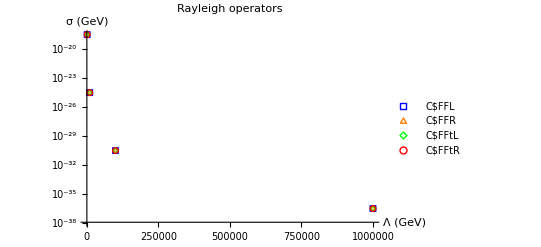

```mathematica
SD$CFFL$List=CS$at$diff$Λ[{SD$mean$CS,SD$stdDev$CS}/.{C$FFL->1,C$FFR->0,C$FFtL->0,C$FFtR->0}];
SD$CFFR$List=CS$at$diff$Λ[{SD$mean$CS,SD$stdDev$CS}/.{C$FFL->0,C$FFR->1,C$FFtL->0,C$FFtR->0}];
SD$CFFtL$List=CS$at$diff$Λ[{SD$mean$CS,SD$stdDev$CS}/.{C$FFL->0,C$FFR->0,C$FFtL->1,C$FFtR->0}];
SD$CFFtR$List=CS$at$diff$Λ[{SD$mean$CS,SD$stdDev$CS}/.{C$FFL->0,C$FFR->0,C$FFtL->0,C$FFtR->1}];

SD$CFFL$approx$graph=LogPlot[SD$mean$CS/.{C$FFL->1,C$FFR->0,C$FFtL->0,C$FFtR->0},{Λ,0,11000},PlotLegends->{"Rayleigh ops avg"},PlotStyle->Blue];

ListLogPlot[{Legended[SD$CFFL$List,"C$FFL"],Legended[SD$CFFR$List,"C$FFR"],Legended[SD$CFFtL$List,"C$FFtL"],Legended[SD$CFFtR$List,"C$FFtR"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"Rayleigh operators",PlotRange->All]
```

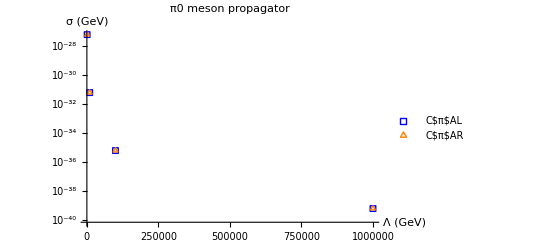

```mathematica
LD$π0$CπAL$List=CS$at$diff$Λ[{LD$π0$mean$CS,LD$π0$stdDev$CS}/.{C$π$AL->1,C$π$AR->0}];
LD$π0$CπAR$List=CS$at$diff$Λ[{LD$π0$mean$CS,LD$π0$stdDev$CS}/.{C$π$AL->0,C$π$AR->1}];

LD$π0$CπAL$approx$graph=LogPlot[LD$π0$mean$CS/.{C$π$AL->1,C$π$AR->0},{Λ,0,11000},PlotLegends->{"π0 meson prop avg"},PlotStyle->Green];

ListLogPlot[{Legended[LD$π0$CπAL$List,"C$π$AL"],Legended[LD$π0$CπAR$List,"C$π$AR"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"π0 meson propagator",PlotRange->All]
```

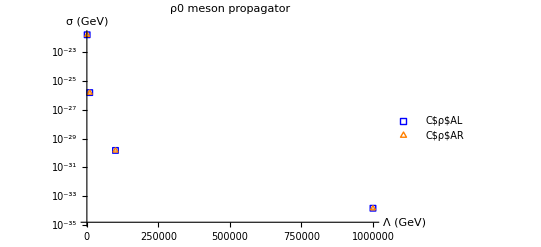

```mathematica
LD$ρ0$CρVL$List=CS$at$diff$Λ[{LD$ρ0$mean$CS,LD$ρ0$stdDev$CS}/.{C$ρ$VL->1,C$ρ$VR->0}];
LD$ρ0$CρVR$List=CS$at$diff$Λ[{LD$ρ0$mean$CS,LD$ρ0$stdDev$CS}/.{C$ρ$VL->0,C$ρ$VR->1}];

LD$ρ0$CρVL$approx$graph=LogPlot[LD$ρ0$mean$CS/.{C$ρ$VL->1,C$ρ$VR->0},{Λ,0,11000},PlotLegends->{"ρ0 meson prop avg"},PlotStyle->Orange];

ListLogPlot[{Legended[LD$ρ0$CρVL$List,"C$ρ$AL"],Legended[LD$ρ0$CρVR$List,"C$ρ$AR"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"ρ0 meson propagator",PlotRange->All]
```

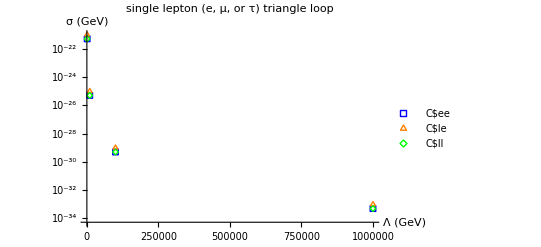

```mathematica
lep$loop$Cee$List=CS$at$diff$Λ[{lep$loop$mean$CS,lep$loop$stdDev$CS}/.{C$ee->1,C$le->0,C$ll->0}];
lep$loop$Cle$List=CS$at$diff$Λ[{lep$loop$mean$CS,lep$loop$stdDev$CS}/.{C$ee->0,C$le->1,C$ll->0}];
lep$loop$Cll$List=CS$at$diff$Λ[{lep$loop$mean$CS,lep$loop$stdDev$CS}/.{C$ee->0,C$le->0,C$ll->1}];

lep$Cee$approx$graph=LogPlot[lep$loop$mean$CS/.{C$ee->1,C$le->0,C$ll->0},{Λ,0,11000},PlotLegends->{"lepton axial ops avg"},PlotStyle->Red];

ListLogPlot[{Legended[lep$loop$Cee$List,"C$ee"],Legended[lep$loop$Cle$List,"C$le"],Legended[lep$loop$Cll$List,"C$ll"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"single lepton (e, μ, or τ) triangle loop",PlotRange->All]
```

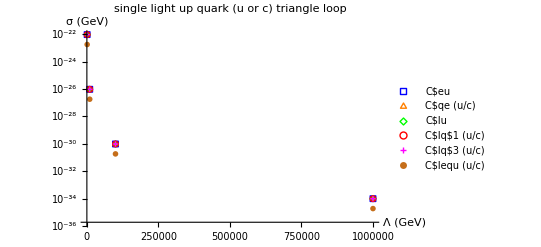

```mathematica
up$loop$Ceu$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->1,C$qe->0,C$lu->0,C$lq$1->0,C$lq$3->0,C$lequ->0}];
up$loop$Cqe$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->0,C$qe->1,C$lu->0,C$lq$1->0,C$lq$3->0,C$lequ->0}];
up$loop$Clu$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->0,C$qe->0,C$lu->1,C$lq$1->0,C$lq$3->0,C$lequ->0}];
up$loop$Clq1$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->0,C$qe->0,C$lu->0,C$lq$1->1,C$lq$3->0,C$lequ->0}];
up$loop$Clq3$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->0,C$qe->0,C$lu->0,C$lq$1->0,C$lq$3->1,C$lequ->0}];
up$loop$Clequ$List=CS$at$diff$Λ[{up$loop$mean$CS,up$loop$stdDev$CS}/.{C$eu->0,C$qe->0,C$lu->0,C$lq$1->0,C$lq$3->0,C$lequ->1}];

up$loop$Ceu$approx$graph=LogPlot[up$loop$mean$CS/.{C$eu->1,C$qe->0,C$lu->0,C$lq$1->0,C$lq$3->0,C$lequ->0},{Λ,0,11000},PlotLegends->{"(u/c) axial ops avg"},PlotStyle->Cyan];
up$loop$Clequ$approx$graph=LogPlot[up$loop$mean$CS/.{C$eu->0,C$qe->0,C$lu->0,C$lq$1->0,C$lq$3->0,C$lequ->1},{Λ,0,11000},PlotLegends->{"(u/c) C$lequ interpolated"},PlotStyle->{Cyan,Dashed}];

ListLogPlot[{Legended[up$loop$Ceu$List,"C$eu"],Legended[up$loop$Cqe$List,"C$qe (u/c)"],Legended[up$loop$Clu$List,"C$lu"],Legended[up$loop$Clq1$List,"C$lq$1 (u/c)"],Legended[up$loop$Clq3$List,"C$lq$3 (u/c)"],Legended[up$loop$Clequ$List,"C$lequ (u/c)"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"single light up quark (u or c) triangle loop",PlotRange->All]
```

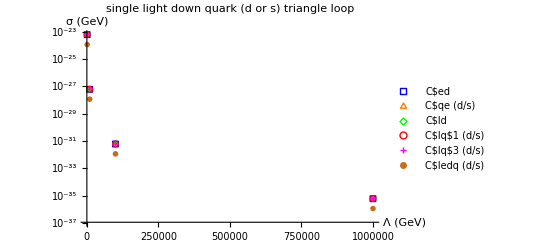

```mathematica
down$loop$Ced$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->1,C$qe->0,C$ld->0,C$lq$1->0,C$lq$3->0,C$ledq->0}];
down$loop$Cqe$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->0,C$qe->1,C$ld->0,C$lq$1->0,C$lq$3->0,C$ledq->0}];
down$loop$Cld$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->0,C$qe->0,C$ld->1,C$lq$1->0,C$lq$3->0,C$ledq->0}];
down$loop$Clq1$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->0,C$qe->0,C$ld->0,C$lq$1->1,C$lq$3->0,C$ledq->0}];
down$loop$Clq3$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->0,C$qe->0,C$ld->0,C$lq$1->0,C$lq$3->1,C$ledq->0}];
down$loop$Cledq$List=CS$at$diff$Λ[{down$loop$mean$CS,down$loop$stdDev$CS}/.{C$ed->0,C$qe->0,C$ld->0,C$lq$1->0,C$lq$3->0,C$ledq->1}];

down$loop$Ced$approx$graph=LogPlot[down$loop$mean$CS/.{C$ed->1,C$qe->0,C$ld->0,C$lq$1->0,C$lq$3->0,C$ledq->0},{Λ,0,11000},PlotLegends->{"(d/s) axial ops avg"},PlotStyle->Magenta];
down$loop$Cledq$approx$graph=LogPlot[down$loop$mean$CS/.{C$ed->0,C$qe->0,C$ld->0,C$lq$1->0,C$lq$3->0,C$ledq->1},{Λ,0,11000},PlotLegends->{"(d/s) C$ledq interpolated"},PlotStyle->{Magenta,Dashed}];

ListLogPlot[{Legended[down$loop$Ced$List,"C$ed"],Legended[down$loop$Cqe$List,"C$qe (d/s)"],Legended[down$loop$Cld$List,"C$ld"],Legended[down$loop$Clq1$List,"C$lq$1 (d/s)"],Legended[down$loop$Clq3$List,"C$lq$3 (d/s)"],Legended[down$loop$Cledq$List,"C$ledq (d/s)"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"single light down quark (d or s) triangle loop",PlotRange->All]
```

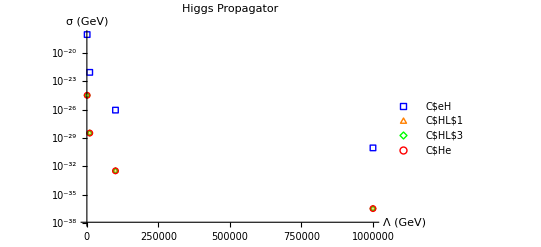

```mathematica
Higgs$CeH$List=CS$at$diff$Λ[{H$mean$CS,H$stdDev$CS}/.{C$eH->1,C$HL$1->0,C$HL$3->0,C$He->0}];
Higgs$CHL1$List=CS$at$diff$Λ[{H$mean$CS,H$stdDev$CS}/.{C$eH->0,C$HL$1->1,C$HL$3->0,C$He->0}];
Higgs$CHL3$List=CS$at$diff$Λ[{H$mean$CS,H$stdDev$CS}/.{C$eH->0,C$HL$1->0,C$HL$3->1,C$He->0}];
Higgs$CHe$List=CS$at$diff$Λ[{H$mean$CS,H$stdDev$CS}/.{C$eH->0,C$HL$1->0,C$HL$3->0,C$He->1}];

ListLogPlot[{Legended[Higgs$CeH$List,"C$eH"],Legended[Higgs$CHL1$List,"C$HL$1"],Legended[Higgs$CHL3$List,"C$HL$3"],Legended[Higgs$CHe$List,"C$He"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"Higgs Propagator",PlotRange->All]
```

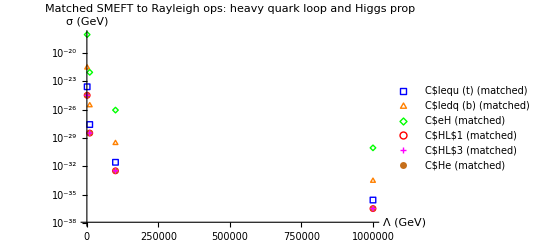

```mathematica
matched$Clequ$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->1,C$ledq->0,C$eH->0,C$HL$1->0,C$HL$3->0,C$He->0}];
matched$Cledq$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->0,C$ledq->1,C$eH->0,C$HL$1->0,C$HL$3->0,C$He->0}];
matched$CeH$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->0,C$ledq->0,C$eH->1,C$HL$1->0,C$HL$3->0,C$He->0}];
matched$CHL1$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->0,C$ledq->0,C$eH->0,C$HL$1->1,C$HL$3->0,C$He->0}];
matched$CHL3$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->0,C$ledq->0,C$eH->0,C$HL$1->0,C$HL$3->1,C$He->0}];
matched$CHe$List=CS$at$diff$Λ[{matched$SD$mean$CS,matched$SD$stdDev$CS}/.{C$lequ->0,C$ledq->0,C$eH->0,C$HL$1->0,C$HL$3->0,C$He->1}];

ListLogPlot[{Legended[matched$Clequ$List,"C$lequ (t) (matched)"],Legended[matched$Cledq$List,"C$ledq (b) (matched)"],Legended[matched$CeH$List,"C$eH (matched)"],Legended[matched$CHL1$List,"C$HL$1 (matched)"],Legended[matched$CHL3$List,"C$HL$3 (matched)"],Legended[matched$CHe$List,"C$He (matched)"]},PlotMarkers->plot$styles,x$y$axes$labels,PlotLabel->"Matched SMEFT to Rayleigh ops: heavy quark loop and Higgs prop",PlotRange->All]
```

### Comparison graphs

```mathematica
axesFont=14;
dataSize=Medium;
x$y$axes$labels=AxesLabel->{"Λ (GeV)","σ ("<>ToString[Superscript["GeV","-2"],StandardForm]<>")"};
plot$styles={Style["□", dataSize, Blue],Style["△", dataSize, Orange],Style["◇", dataSize, Green],Style["○", dataSize, Red],Style["+", dataSize, Magenta],Style["x", dataSize, Cyan]};
```

```mathematica
File$Location="C:\\Users\\cgran\\Dropbox\\mu to e nucleus conversion\\paper\\CS plots\\";
Plot$Range={{5*10^2,0.5*10^7},All};
```

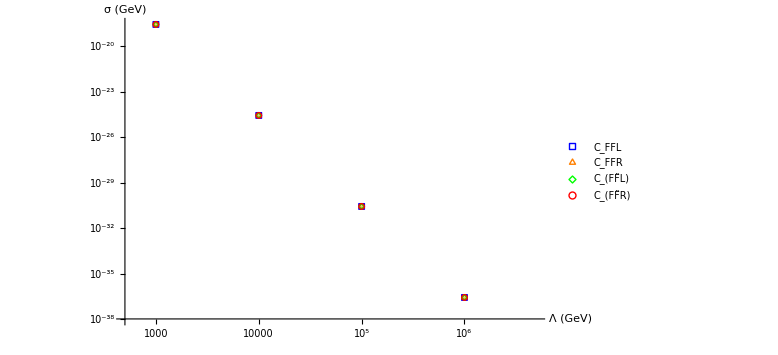

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\RO_CS.pdf

```mathematica
RO$plot=ListLogLogPlot[{Legended[SD$CFFL$List,Style[ToString[Subscript["C","FFL"],StandardForm],axesFont]],Legended[SD$CFFR$List,Style[ToString[Subscript["C","FFR"],StandardForm],axesFont]],Legended[SD$CFFtL$List,Style[ToString[Subscript["C","F"<>ToString[OverTilde["F"],StandardForm]<>"L"],StandardForm],axesFont]],Legended[SD$CFFtR$List,Style[ToString[Subscript["C","F"<>ToString[OverTilde["F"],StandardForm]<>"R"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"RO_CS.pdf",RO$plot]
```

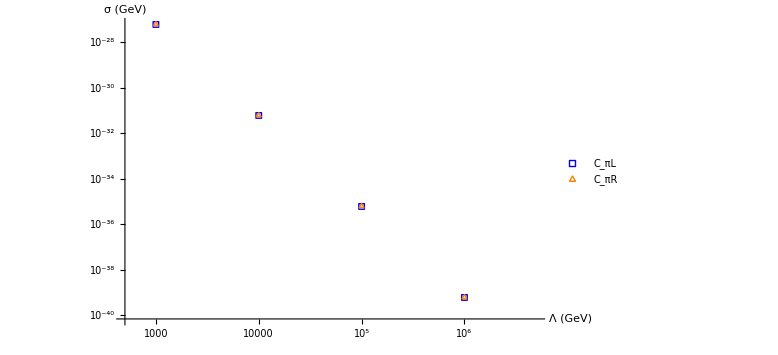

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\pion_CS.pdf

```mathematica
π0$plot=ListLogLogPlot[{Legended[LD$π0$CπAL$List,Style[ToString[Subscript["C","πL"],StandardForm],axesFont]],Legended[LD$π0$CπAR$List,Style[ToString[Subscript["C","πR"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"pion_CS.pdf",π0$plot]
```

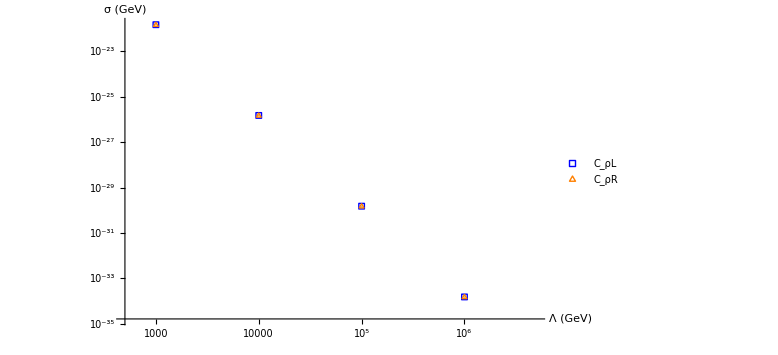

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\rho_CS.pdf

```mathematica
ρ0$plot=ListLogLogPlot[{Legended[LD$ρ0$CρVL$List,Style[ToString[Subscript["C","ρL"],StandardForm],axesFont]],Legended[LD$ρ0$CρVR$List,Style[ToString[Subscript["C","ρR"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"rho_CS.pdf",ρ0$plot]
```

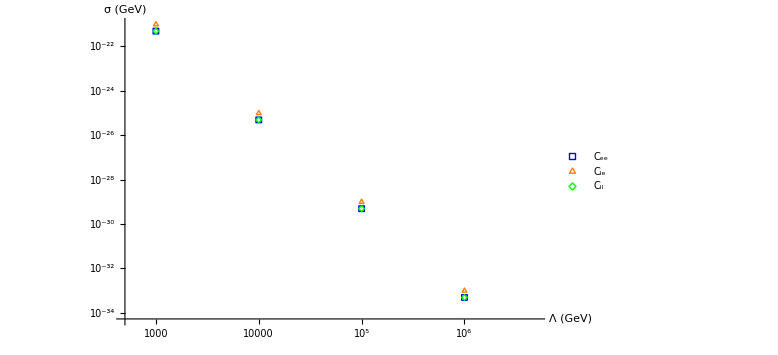

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\lep_CS.pdf

```mathematica
lep$plot=ListLogLogPlot[{Legended[lep$loop$Cee$List,Style[ToString[Subscript["C","ee"],StandardForm],axesFont]],Legended[lep$loop$Cle$List,Style[ToString[Subscript["C","le"],StandardForm],axesFont]],Legended[lep$loop$Cll$List,Style[ToString[Subscript["C","ll"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"lep_CS.pdf",lep$plot]
```

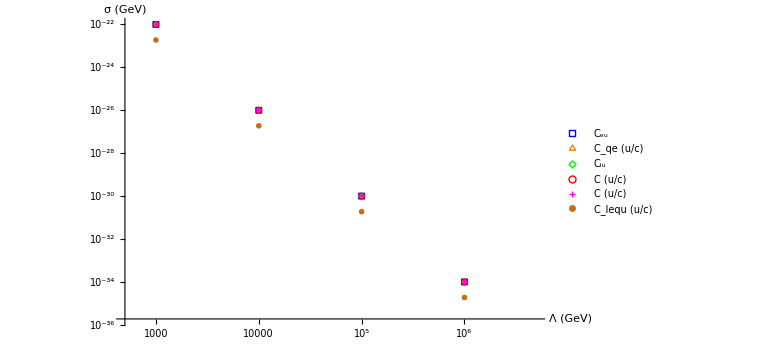

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\u_CS.pdf

```mathematica
u$plot=ListLogLogPlot[{Legended[up$loop$Ceu$List,Style[ToString[Subscript["C","eu"],StandardForm],axesFont]],Legended[up$loop$Cqe$List,Style[ToString[Subscript["C","qe"],StandardForm]<>"  (u/c)",axesFont]],Legended[up$loop$Clu$List,Style[ToString[Subscript["C","lu"],StandardForm],axesFont]],Legended[up$loop$Clq1$List,Style[ToString[Subsuperscript["C","lq","(1)"],StandardForm]<>"  (u/c)",axesFont]],Legended[up$loop$Clq3$List,Style[ToString[Subsuperscript["C","lq","(3)"],StandardForm]<>"  (u/c)",axesFont]],Legended[up$loop$Clequ$List,Style[ToString[Subscript["C","lequ"],StandardForm]<>"  (u/c)",axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"u_CS.pdf",u$plot]
```

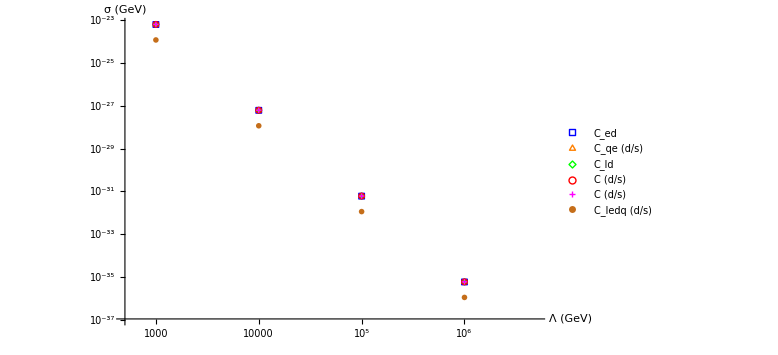

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\d_CS.pdf

```mathematica
d$plot=ListLogLogPlot[{Legended[down$loop$Ced$List,Style[ToString[Subscript["C","ed"],StandardForm],axesFont]],Legended[down$loop$Cqe$List,Style[ToString[Subscript["C","qe"],StandardForm]<>"  (d/s)",axesFont]],Legended[down$loop$Cld$List,Style[ToString[Subscript["C","ld"],StandardForm],axesFont]],Legended[down$loop$Clq1$List,Style[ToString[Subsuperscript["C","lq","(1)"],StandardForm]<>"  (d/s)",axesFont]],Legended[down$loop$Clq3$List,Style[ToString[Subsuperscript["C","lq","(3)"],StandardForm]<>"  (d/s)",axesFont]],Legended[down$loop$Cledq$List,Style[ToString[Subscript["C","ledq"],StandardForm]<>"  (d/s)",axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"d_CS.pdf",d$plot]
```

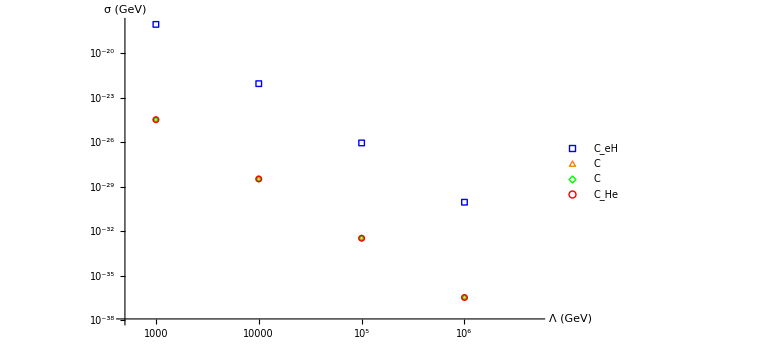

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\H_CS.pdf

```mathematica
Higgs$plot=ListLogLogPlot[{Legended[Higgs$CeH$List,Style[ToString[Subscript["C","eH"],StandardForm],axesFont]],Legended[Higgs$CHL1$List,Style[ToString[Subsuperscript["C","Hl","(1)"],StandardForm],axesFont]],Legended[Higgs$CHL3$List,Style[ToString[Subsuperscript["C","Hl","(3)"],StandardForm],axesFont]],Legended[Higgs$CHe$List,Style[ToString[Subscript["C","He"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"H_CS.pdf",Higgs$plot]
```

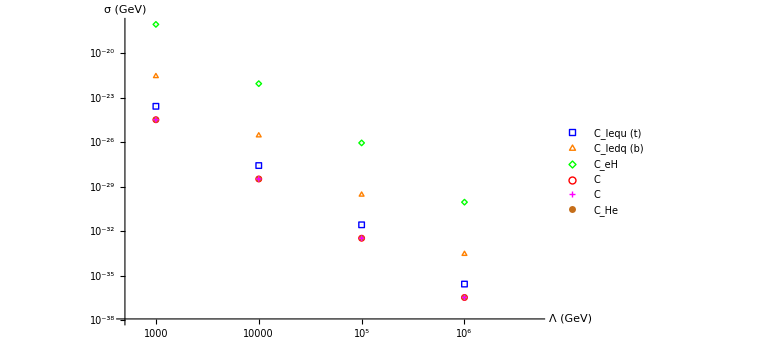

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\matched_CS.pdf

```mathematica
matched$plot=ListLogLogPlot[{Legended[matched$Clequ$List,Style[ToString[Subscript["C","lequ"],StandardForm]<>"  (t)",axesFont]],Legended[matched$Cledq$List,Style[ToString[Subscript["C","ledq"],StandardForm]<>"  (b)",axesFont]],Legended[matched$CeH$List,Style[ToString[Subscript["C","eH"],StandardForm],axesFont]],Legended[matched$CHL1$List,Style[ToString[Subsuperscript["C","Hl","(1)"],StandardForm],axesFont]],Legended[matched$CHL3$List,Style[ToString[Subsuperscript["C","Hl","(3)"],StandardForm],axesFont]],Legended[matched$CHe$List,Style[ToString[Subscript["C","He"],StandardForm],axesFont]]},PlotMarkers->plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"matched_CS.pdf",matched$plot]
```

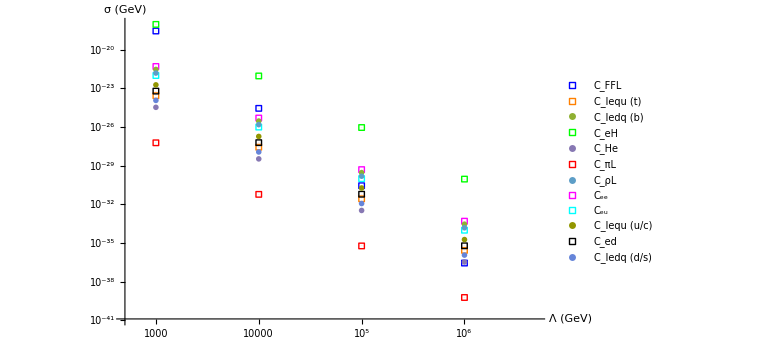

C:\Users\cgran\Dropbox\mu to e nucleus conversion\paper\CS plots\All_CS.pdf

```mathematica
all$plots={Legended[SD$CFFL$List,Style[ToString[Subscript["C","FFL"],StandardForm],axesFont]],Legended[matched$Clequ$List,Style[ToString[Subscript["C","lequ"],StandardForm]<>"  (t)",axesFont]],Legended[matched$Cledq$List,Style[ToString[Subscript["C","ledq"],StandardForm]<>"  (b)",axesFont]],Legended[matched$CeH$List,Style[ToString[Subscript["C","eH"],StandardForm],axesFont]],Legended[matched$CHe$List,Style[ToString[Subscript["C","He"],StandardForm],axesFont]],Legended[LD$π0$CπAL$List,Style[ToString[Subscript["C","πL"],StandardForm],axesFont]],Legended[LD$ρ0$CρVL$List,Style[ToString[Subscript["C","ρL"],StandardForm],axesFont]],Legended[lep$loop$Cee$List,Style[ToString[Subscript["C","ee"],StandardForm],axesFont]],Legended[up$loop$Ceu$List,Style[ToString[Subscript["C","eu"],StandardForm],axesFont]],Legended[up$loop$Clequ$List,Style[ToString[Subscript["C","lequ"],StandardForm]<>"  (u/c)",axesFont]],Legended[down$loop$Ced$List,Style[ToString[Subscript["C","ed"],StandardForm],axesFont]],Legended[down$loop$Cledq$List,Style[ToString[Subscript["C","ledq"],StandardForm]<>"  (d/s)",axesFont]]};

all$plot$styles={Style["□", dataSize, Blue],Style["□", dataSize, Orange],Style["x", dataSize, Orange],Style["□", dataSize, Green],Style["x", dataSize, Green],Style["□", dataSize, Red],Style["x", dataSize, Red],Style["□", dataSize, Magenta],Style["□", dataSize, Cyan],Style["x", dataSize, Cyan],Style["□", dataSize, Black],Style["x", dataSize, Black]};

All$plot=ListLogLogPlot[all$plots, PlotMarkers->all$plot$styles,x$y$axes$labels,PlotRange->Plot$Range,TicksStyle->axesFont,AxesStyle->axesFont,ImageSize->Large]
Export[File$Location<>"All_CS.pdf",All$plot]
```